```mathematica
Lecture 3:Apply,Logic, If, Select
```

## Heads and Apply

### Exercise Subsection

Use FullForm and TreeForm and Head on each of these expressions:
a. 2*Sin[Pi*x] - Cos[Pi*x]
b. {x,y,z}
c. x+y+z

```mathematica
FullForm[2*Sin[Pi*x] - Cos[Pi*x]]
```

Plus[Times[-1,Cos[Times[Pi,x]]],Times[2,Sin[Times[Pi,x]]]]

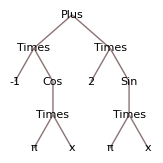

Plus

```mathematica
TreeForm[2*Sin[Pi*x] - Cos[Pi*x]]
Head[2*Sin[Pi*x] - Cos[Pi*x]]
```

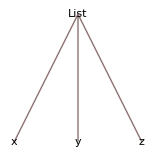

List

```mathematica
TreeForm[{x,y,z}]
Head@{x,y,z}
```

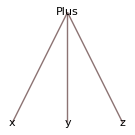

Plus

```mathematica
TreeForm[x+y+z]
Head@(x+y+z)
```

```mathematica
?Apply
```

```mathematica
Apply[Plus,{x,y,z}]
```

x+y+z

```mathematica
Head[x y z]
Apply[List,x y z]
```

Times

{x,y,z}

### Exercise Subsection

Use Apply (or @@) to define the a function that sums the first n positive integers that are multiples of 7 and then evaluate this function at 1000.

```mathematica
f[n_]:=Plus@@(7 Range@n)
```

```mathematica
Head[f[2]]
```

Integer

### Exercise Subsection

Use Apply and the listable property of the arithmetic operations on Range@n to create a function named PartialSum with input n and output the numerical value of 1/1 - 1/2 + 1/3 - 1/4 + ... +/- 1/n.  Then Map this function to the first 1000 integers.

```mathematica
PartialSum[n_]:=Plus@@((-1)^(Range@n-1)/Range@n)//N
```

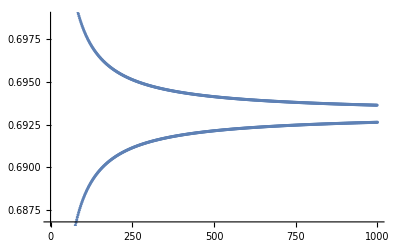

```mathematica
PartialSum/@Range@1000//ListPlot
```

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Plus@@Fibonacci@Range@100
```

927372692193078999175

This sums the first 100 Fibonacci numbers.

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Table[Times@@Range[1,n,2],{n,20}]
```

{1,1,3,3,15,15,105,105,945,945,10395,10395,135135,135135,2027025,2027025,34459425,34459425,654729075,654729075}

The nth element on the output list is the product of the odd numbers up to n.

## Logic

### Exercise Subsection

What does the following cell do when evaluated?  How will the output change if “Or” is replaced with “And”?  What if “Or” is replaced with “Implies”?

```mathematica
Map[Apply[Or,#]&,{{True,True},{True,False},{False,True},{False,False}}]
Or@@@{{True,True},{True,False},{False,True},{False,False}}
```

{True,True,True,False}

{True,True,True,False}

```mathematica
And@@@{{True,True},{True,False},{False,True},{False,False}}
```

{True,False,False,False}

### Exercise Subsection

Show that “P implies Q” and the contrapositive “not Q implies not P” are logically equivalent by showing each expression gives the same output for each possible Boolean (True or False) input for P and Q.

```mathematica
Implies@@@Tuples[{True,False},2]
```

{True,False,True,True}

```mathematica
Implies@@@(Not/@#&/@Reverse/@Tuples[{True,False},2])
```

{True,False,True,True}

```mathematica
Implies@@@(Not/@#&/@Reverse/@Tuples[{True,False},2])==Implies@@@Tuples[{True,False},2]
```

True

```mathematica
Reverse/@Tuples[{True,False},2]
```

{{True,True},{False,True},{True,False},{False,False}}

### Exercise Subsection

What does the following cell do when evaluated?  Then find an number to replace “Sqrt[-41]” such that the output has exactly one False.

```mathematica
Element[Sqrt[-41],#]&/@{Primes,Integers,Rationals,Reals,Algebraics,Complexes}
```

{False,False,False,False,True,True}

```mathematica
Element[6,#]&/@{Primes,Integers,Rationals,Reals,Algebraics,Complexes}
```

{False,True,True,True,True,True}

### Exercise Subsection

Create a function that takes in a string and then outputs True if the string starts or ends with “z” and has at least 8 letters.  (See Characters.)

```mathematica
Characters@"This is a string of text."
```

{T,h,i,s, ,i,s, ,a, ,s,t,r,i,n,g, ,o,f, ,t,e,x,t,.}

```mathematica
Zchecker[s_]:=And[Or[First@Characters@s=="z",Last@Characters@s=="z"],Length@Characters@s>=8]
```

```mathematica
Zchecker["z3333313gsvsd"]
```

True

## If

### Exercise Subsection

Define a function ReciprocalPrime that outputs 1/n if the integer n is prime and 0 otherwise.  Then find the numerical value of the sum of ReciprocalPrime for the first 10^6 positive integers.

```mathematica
ReciprocalPrime[n_]:=If[PrimeQ@n,1/n,0]
```

```mathematica
Plus@@(ReciprocalPrime/@Range[10^6])//N
```

2.88733

```mathematica
ReciprocalPrime[5]
```

1/5

### Exercise Subsection

Define a function with input the real number x and output Sqrt[1-x^2]if x is between -1 and 1 and 0 otherwise.

```mathematica
f[x_]:=If[-1<=x<=1,Sqrt[1-x^2],0]
```

### Exercise Subsection

Use Which to define a function with input the list L of real numbers and output the list L with every number larger than 1 replaced with 1 and every number smaller than -1 replaced with -1.

```mathematica
helper[n_]:=Which[n>=1,1,n<=-1,-1,True,n]
f[L_]:=helper/@L
```

```mathematica
f[L_]:=Which[#>=1,1,#<=-1,-1,True,#]&/@L
```

```mathematica
f[{-3,3,1/2,1/4,1,6}]
```

{-1,1,1/2,1/4,1,1}

### Exercise Subsection

Use Which to define a function with input the list L and output the list L with each sublist in L replaced by its length and every other element in L left unchanged (see ListQ).

```mathematica
helper[L_]:=Which[ListQ@L,Length@L,True,L]
f[L_]:=helper/@L
```

```mathematica
f[{{1,2,3},4,45,{4,4,1,1,1}}]
```

{3,4,45,5}

## Select

### Exercise Subsection

Use Select to create a list of all prime numbers of the form 2^n-1 for n <= 1000.  How many such integers n are there?

```mathematica
Select[2^Range@1000-1,PrimeQ]
```

{3,7,31,127,8191,131071,524287,2147483647,2305843009213693951,618970019642690137449562111,162259276829213363391578010288127,170141183460469231731687303715884105727,6864797660130609714981900799081393217269435300143305409394463459185543183397656052122559640661454554977296311391480858037121987999716643812574028291115057151,531137992816767098689588206552468627329593117727031923199444138200403559860852242739162502265229285668889329486246501015346579337652707239409519978766587351943831270835393219031728127}

### Exercise Subsection

Use Select together with IntegerQ to give the list of positive integers n less than 100 such that n^3 + n + 51 is a perfect square.

```mathematica
n=Range@100
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Select[Sqrt[n^3+n+51],IntegerQ]
```

{9,53}

```mathematica
Select[Range@100,IntegerQ@Sqrt@(#^3+#+51)&]
```

{3,14}

### Exercise Subsection

Give a list of positive integers less than 10^6 have digits that sum to 4.  It may help to use the functions IntegerDigits and Total.

### Exercise Subsection

Give a list with nth element of the number of primes between n and n^2 for 1 <= n <= 100.

### Exercise Subsection

Use the list of words in WordList and the function StringLength to find a list of words that have more than 19 letters.

```mathematica
Select[WordList[],StringLength@#>19&]
```

{buckminsterfullerene,compartmentalization,counterrevolutionary,electroencephalogram,electroencephalograph,electroencephalographic,internationalization,magnetohydrodynamics,uncharacteristically}

### Exercise Subsection

Find words in WordList that are the same as their StringReverse.  (To check if two expressions A and B are equal, use A==B.)

```mathematica
Select[WordList[],StringReverse@#==#&]
```

{a,aha,bib,bob,civic,dad,deed,did,dud,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,pop,pup,radar,refer,rotor,sis,tat,tenet,TNT,toot,tot,tut,wow}

### Exercise Subsection

How may words in WordList[] contain consecutive identical letters?

```mathematica
helper[s_]:=Or@@Table[(Characters@s)[[i]]==(Characters@s)[[i+1]],{i,1,Length@Characters@s-1}]
Select[WordList[],helper]
```

{aah,aardvark,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,aberrant,aberration,abettor,abhorrence,abhorrent,abloom,abnormally,abrasiveness,abruptness,abscess,abscessed,abscissa,abscission,absentee,absenteeism,absentmindedness,absoluteness,abstemiousness,abstractedness,abstractness,abstruseness,abuzz,abysmally,abyss,abyssal,academically,accede,accelerate,accelerated,acceleration,accelerator,accelerometer,accent,accented,accenting,accentual,accentuate,accentuation,accept,acceptability,acceptable,acceptableness,acceptably,acceptance,acceptation,accepted,accepting,acceptor,access,accessibility,accessible,accession,accessory,accidence,accident,accidental,accidentally,acclaim,acclamation,acclimate,acclimation,acclimatisation,acclimatise,acclimatization,acclimatize,acclivity,accolade,accommodate,accommodating,accommodatingly,accommodation,accompanied,accompaniment,accompanist,accompany,accompanying,accomplice,accomplish,accomplished,accomplishment,accord,accordance,accordant,according,accordingly,accordion,accordionist,accost,account,accountability,accountable,accountancy,accountant,accounting,accoutered,accoutrement,accredit,accreditation,accredited,accretion,accrual,accrue,accrued,acculturate,acculturation,accumulate,accumulated,accumulation,accumulative,accumulator,accuracy,accurate,accurately,accursed,accusation,accusative,accusatory,accuse,accused,accuser,accusing,accusingly,accustom,accustomed,acoustically,acquisitiveness,acquittal,acquittance,acquitted,across,activeness,actress,actually,acupressure,acuteness,add,addend,addendum,adder,addict,addicted,addiction,addictive,addition,additional,additionally,additive,addle,addled,add-on,address,addressable,addressed,addressee,adduce,adducing,adeptness,adequateness,adhesiveness,adjectivally,admissibility,admissible,admission,admittance,admittedly,adroitness,adulthood,adventuress,adventurousness,adverbially,aerially,aesthetically,affability,affable,affably,affair,affairs,affect,affectation,affected,affectedly,affecting,affectingly,affection,affectionate,affectionately,affective,afferent,affiance,affidavit,affiliate,affiliated,affiliation,affine,affinity,affirm,affirmation,affirmative,affirmatively,affix,affixed,afflatus,afflict,afflicted,affliction,affluence,affluent,afford,affordable,afforest,afforestation,affray,affront,aflutter,afoot,aftereffect,afternoon,ageless,agelessness,agglomerate,agglomerated,agglomeration,agglutinate,agglutination,agglutinative,aggrandize,aggrandizement,aggravate,aggravated,aggravating,aggravatingly,aggravation,aggregate,aggregated,aggregation,aggression,aggressive,aggressively,aggressiveness,aggressor,aggrieve,aggro,aglitter,agree,agreeable,agreeableness,agreeably,agreed,agreement,agribusiness,aigrette,aimless,aimlessly,aimlessness,airiness,airless,airsickness,airspeed,airworthiness,albatross,alertness,algebraically,aliveness,all,allay,allegation,allege,alleged,allegedly,allegiance,allegoric,allegorical,allegorically,allegory,allegretto,allegro,allele,allelic,alleluia,allergen,allergenic,allergic,allergist,allergy,alleviate,alleviated,alleviation,alley,alleyway,alliance,allied,allies,alligator,alliterate,alliteration,alliterative,alliteratively,allocatable,allocate,allocation,allocator,allot,allotment,allotrope,allotropic,allotted,allover,allow,allowable,allowably,allowance,alloy,alloyed,allspice,allude,allure,allurement,alluring,allusion,allusive,allusiveness,alluvial,alluvium,ally,aloof,aloofness,alphabetically,altruistically,amaretto,amaryllis,amass,amateurishness,ambassador,ambassadorial,ambassadorship,ambassadress,ambitiousness,amiableness,amiss,ammeter,ammo,ammonia,ammonium,ammunition,amorally,amputee,anachronistically,anagrammatic,analytically,anarchically,anatomically,ancestress,ancientness,ancillary,angelically,aniseed,anisette,annalist,annals,anneal,annealing,annelid,annex,annexation,annexe,annihilate,annihilated,annihilating,annihilation,annihilator,anniversary,annotate,annotating,annotation,annotator,announce,announced,announcement,announcer,annoy,annoyance,annoyed,annoying,annoyingly,annual,annually,annuitant,annuity,annul,annular,annulment,annulus,annunciation,antagonistically,antebellum,antenna,anteroom,anthill,antidepressant,antifreeze,antimacassar,antimatter,antipersonnel,antipollution,antithetically,anxiousness,apathetically,apogee,apologetically,appall,appalled,appalling,appallingly,apparatchik,apparatus,apparel,appareled,apparent,apparently,apparition,appeal,appealing,appealingly,appear,appearance,appearing,appease,appeasement,appeaser,appeasing,appellant,appellate,appellation,append,appendage,appendectomy,appendicitis,appendix,appertain,appetite,appetizer,appetizing,applaud,applause,apple,applecart,applejack,applesauce,applet,appliance,applicability,applicable,applicant,application,applicative,applicator,applied,applier,applique,apply,appoint,appointed,appointee,appointive,appointment,apportion,apportioned,apportioning,apportionment,appose,apposite,appositeness,apposition,appositive,appraisal,appraise,appraiser,appraising,appreciable,appreciably,appreciate,appreciated,appreciation,appreciative,appreciatively,appreciator,apprehend,apprehended,apprehension,apprehensive,apprehensively,apprehensiveness,apprentice,apprenticed,apprenticeship,apprise,approach,approachability,approachable,approaching,approbation,appropriate,appropriately,appropriateness,appropriation,appropriator,approval,approve,approved,approving,approvingly,approximate,approximately,approximation,appurtenance,appurtenant,aptness,arbitrariness,archduchess,architecturally,archness,arduousness,aristocratically,arithmetically,armadillo,armless,arpeggio,arraign,arraignment,arrange,arranged,arrangement,arranger,arranging,arrant,arras,array,arrayed,arrears,arrest,arresting,arrhythmia,arrhythmic,arrival,arrive,arrogance,arrogant,arrogantly,arrogate,arrogation,arrow,arrowhead,arrowroot,arroyo,artfully,artfulness,articulateness,artificially,artillery,artilleryman,artistically,artless,artlessly,artlessness,ascetically,ASCII,asexually,asleep,assail,assailable,assailant,assassin,assassinate,assassinated,assassination,assault,assaulter,assay,assayer,assemblage,assemble,assembler,assembling,assembly,assemblyman,assent,assenting,assert,asserted,asserting,assertion,assertive,assertively,assertiveness,assess,assessable,assessment,assessor,asset,assets,asseverate,asseveration,assiduity,assiduous,assiduously,assiduousness,assign,assignable,assignation,assigned,assigning,assignment,assignor,assimilable,assimilate,assimilating,assimilation,assist,assistance,assistant,assisted,assize,assizes,associate,associateship,association,associational,associative,assonance,assonant,assort,assorted,assortment,assuage,assume,assumed,assuming,assumption,assumptive,assurance,assure,assured,assuredly,assuring,astraddle,astronomically,astuteness,asymmetric,asymmetrical,asymmetrically,asymmetry,asymptotically,atoll,atrociousness,attach,attachable,attache,attached,attachment,attack,attacker,attacking,attain,attainability,attainable,attainder,attained,attainment,attar,attempt,attempted,attend,attendance,attendant,attended,attendee,attender,attending,attention,attentional,attentive,attentively,attentiveness,attenuate,attenuated,attenuation,attenuator,attest,attestation,attested,attic,attire,attired,attitude,attitudinal,attorney,attract,attraction,attractive,attractively,attractiveness,attractor,attributable,attribute,attribution,attributive,attributively,attrition,attune,atypically,auctioneer,audaciousness,aurally,auspiciousness,authentically,authoress,autocratically,autoimmune,autoimmunity,automatically,autosuggestion,avariciousness,awareness,awfully,awfulness,awkwardness,axially,axillary,axiomatically,axletree,ayatollah,baa,baas,babble,babbler,babbling,baboon,babyhood,babysitter,babysitting,baccalaureate,baccarat,bacchanal,bacchanalia,bacchanalian,baccy,bachelorhood,bacillary,bacillus,backdoor,backgammon,backless,backroom,backwardness,backwoods,backwoodsman,baddie,badness,baffle,baffled,bafflement,baffling,bagatelle,baggage,bagging,baggy,baguette,bailiff,baksheesh,baldness,baleen,balefully,ball,ballad,ballade,balladeer,ballast,ballcock,ballerina,ballet,balletic,ballgame,ballistic,ballistics,balloon,ballooning,balloonist,ballot,balloting,ballpark,ballplayer,ballpoint,ballroom,bally,ballyhoo,balminess,bamboo,bamboozle,bandanna,bandoleer,bankbook,bankroll,banned,banner,banning,bannock,banns,banquette,banshee,barbell,barberry,barefoot,barefooted,barelegged,bareness,barkeep,barkeeper,baroness,barrack,barracking,barracuda,barrage,barred,barrel,barreled,barrels,barren,barrenness,barrette,barricade,barricaded,barrier,barring,barrio,barrister,barroom,barrow,baseball,baseless,baseness,bashfully,bashfulness,basically,basketball,bass,basset,bassinet,bassist,basso,bassoon,bassoonist,basswood,bathhouse,bathroom,battalion,batten,batter,battered,battering,battery,batting,battle,battledore,battlefield,battlefront,battleground,battlement,battler,battleship,batty,bawdiness,bayberry,bazaar,bazooka,beachhead,beardless,beastliness,beautifully,bedazzle,bedded,bedder,bedding,bedfellow,bedimmed,bedraggled,bedridden,bedroll,bedroom,bedsitter,bee,beech,beechnut,beechwood,beef,beefcake,beefsteak,beefy,beehive,beekeeper,beekeeping,beeline,been,beep,beeper,beer,beery,beeswax,beet,beetle,beetling,beetroot,befall,befitting,befittingly,befogged,befuddle,befuddled,befuddlement,begetter,beggar,beggarly,beggary,begging,beginner,beginning,begotten,behoove,belittle,belittled,belittling,bell,belladonna,bellboy,belle,belletristic,bellhop,bellicose,bellicosity,bellied,belligerence,belligerency,belligerent,belligerently,belling,bellman,bellow,bellowing,bellows,bellwether,belly,bellyache,bellybutton,bellyful,bellying,benefactress,beneficially,bentwood,berried,berry,berrylike,beryllium,beseech,beseeching,beseechingly,beseem,besotted,bespatter,bestially,bestseller,better,bettering,betterment,betting,bettor,between,biannual,biannually,bicentennial,biddable,bidder,bidding,biddy,biennial,biennially,biff,bigger,biggish,bigness,bilaterally,bilberry,bilingually,biliousness,bill,billboard,billed,billet,billfold,billhook,billiard,billiards,billing,billingsgate,billion,billionaire,billionth,billow,billowing,billowy,billy,bimetallic,bimetallism,bindweed,binnacle,biochemically,bioengineering,biofeedback,biologically,biomass,birdseed,biretta,bitter,bitterly,bittern,bitterness,bitters,bittersweet,bitty,biweekly,bizarre,bizarreness,blabber,blabbermouth,blackball,blackberry,blackness,bladder,blameless,blamelessly,blamelessness,blameworthiness,blandness,blankness,blastoff,bleakness,bleed,bleeder,bleeding,bleep,bless,blessed,blessedly,blessedness,blessing,blindness,bliss,blissful,blissfully,blissfulness,blitheness,blizzard,blondness,blood,bloodbath,bloodcurdling,blooded,bloodhound,bloodily,bloodiness,bloodless,bloodlessly,bloodletting,bloodline,bloodshed,bloodshot,bloodstain,bloodstained,bloodstock,bloodstone,bloodstream,bloodsucker,bloodsucking,bloodthirstiness,bloodthirsty,bloodworm,bloody,bloom,bloomer,bloomers,blooming,blooper,blossom,blossoming,blotter,blotto,blubber,blubbery,bluebell,blueberry,bluebonnet,bluebottle,blue-collar,bluegill,bluegrass,blueness,bluff,bluffer,bluffly,bluffness,blunderbuss,bluntness,blurred,blurriness,blurry,boardroom,boastfully,boastfulness,bobbin,bobble,bobby,bobsledding,boccie,bodiless,boffin,boffo,boggle,boggy,boisterousness,boldness,boll,bollard,bombastically,bombproof,bombshell,boneless,boniness,bonnet,bonnie,bonny,boo,booby,boodle,booger,boogie,book,bookable,bookbinder,bookbinding,bookcase,booked,bookend,bookie,booking,bookish,bookkeeper,bookkeeping,booklet,bookmaker,bookmark,bookmobile,bookplate,bookseller,bookshelf,bookshop,bookstall,bookstore,bookworm,boom,boomer,boomerang,booming,boon,boondocks,boondoggle,boor,boorish,boorishly,boorishness,boost,booster,boot,bootblack,booted,booth,bootlace,bootleg,bootlegger,bootlegging,bootless,bootstrap,booty,booze,boozer,boozing,boozy,borrow,borrower,borrowing,boss,bossism,bossy,bottle,bottleneck,bottler,bottom,bottomed,bottomless,bottommost,bouffant,bougainvillea,bouillabaisse,bouillon,boundedness,boundless,boundlessly,boundlessness,bountifully,bountifulness,boutonniere,bowlegged,boxwood,boycott,boyhood,boyishness,boysenberry,braggadocio,braggart,bragging,braille,brainless,brashness,brass,brasserie,brassiere,brassy,bratty,braveness,brazenness,breadwinner,breastfeed,breathless,breathlessly,breathlessness,breech,breeches,breed,breeder,breeding,breeze,breezily,breeziness,breezy,bridegroom,briefness,brightness,brill,brilliance,brilliancy,brilliant,brilliantine,brilliantly,brimless,brimming,briquette,briskness,brittle,brittleness,broadloom,broadness,broadsheet,broccoli,brochette,brolly,brooch,brood,brooder,brooding,broodmare,broody,brook,brooklet,broom,broomstick,brotherhood,brownness,brunette,brushwood,brusqueness,brutally,bubble,bubbling,bubbly,buccaneer,buccaneering,buckaroo,buckminsterfullerene,budding,buddy,buff,buffalo,buffer,buffet,buffeted,buffeting,buffoon,buffoonery,buffoonish,bugaboo,bugged,buggy,bulkiness,bull,bulldog,bulldoze,bulldozer,bullet,bulletin,bulletproof,bullfight,bullfighter,bullfighting,bullfinch,bullfrog,bullhead,bullheaded,bullheadedness,bullhorn,bullion,bullish,bullock,bullpen,bullring,bully,bullying,bumblebee,bummer,bumpiness,bumptiousness,bungee,bunny,bureaucratically,burnoose,burr,burred,burrito,burro,burrow,business,businesslike,businessman,businessmen,businesspeople,businessperson,businesswoman,buss,busyness,butt,butte,butter,butterball,buttercup,butterfat,butterfly,buttermilk,butternut,butterscotch,buttery,buttock,buttocks,button,buttoned,buttonhole,buttonwood,buttress,buttressed,buttressing,butty,buzz,buzzard,buzzer,buzzing,buzzword,bypass,cabbage,caboodle,caboose,caddish,caddy,caff,caffeine,caisson,caitiff,call,calla,callable,callback,caller,calligrapher,calligraphic,calligraphist,calligraphy,calling,calliope,callosity,callous,calloused,callously,callousness,callow,callowness,callus,calmness,camellia,cancellation,candidness,candyfloss,canned,cannelloni,cannery,cannibal,cannibalism,cannibalistic,cannibalize,cannily,cannon,cannonade,cannonball,cannula,canny,canonically,canteen,canvass,canvasser,canvassing,capaciousness,capillarity,capillary,capped,cappuccino,capriciousness,carburettor,carcass,careen,career,careerism,careerist,carefree,carefully,carefulness,careless,carelessly,carelessness,caress,caressing,carillon,carnally,carpetbagger,carpetbagging,carrel,carriage,carriageway,carrier,carrion,carrot,carroty,carry,carryall,cartoon,cartoonist,cartwheel,casebook,cassava,casserole,cassette,cassia,cassock,cassowary,castellated,casually,casualness,catarrh,catastrophically,catcall,catchall,catchpenny,categorically,caterpillar,cattail,cattiness,cattle,cattleman,catty,caudally,causally,causeless,caustically,cautiousness,cayenne,ceaseless,ceaselessly,cedilla,cell,cellar,cellist,cello,cellophane,cellphone,cellular,cellulite,celluloid,cellulose,centennial,centrally,cerebellar,cerebellum,ceremonially,ceremoniousness,cessation,cession,cesspit,cesspool,chaff,chaffinch,challenge,challenger,challenging,challis,chancellery,chancellor,chancellorship,changeableness,changeless,channel,channelization,channelize,channels,chaotically,chaparral,chapatti,chapped,characteristically,characterless,charioteer,charitableness,chassis,chasteness,chattel,chatter,chatterbox,chatterer,chattering,chattily,chatty,chauffeur,cheapness,checkbook,checkroom,cheddar,cheek,cheekbone,cheekily,cheekiness,cheeky,cheep,cheer,cheerer,cheerful,cheerfully,cheerfulness,cheerily,cheering,cheerio,cheerleader,cheerless,cheerlessly,cheerlessness,cheers,cheery,cheese,cheeseburger,cheesecake,cheesecloth,cheeseparing,cheesy,cheetah,chemically,chenille,cheroot,cherry,chess,chessboard,chessman,chickadee,chickweed,chiffon,chiffonier,chigger,childhood,childishness,childless,childlessness,childproof,chill,chiller,chilliness,chilling,chilly,chimpanzee,chinchilla,chinless,chipper,chipping,chirrup,chitterlings,chivvy,chlorophyll,chokecherry,choose,chooser,choosy,chopped,chopper,choppiness,choppy,chorally,chromatically,chronically,chronologically,chubbiness,chubby,chuff,chuffed,chukka,chumminess,chummy,cigarette,cigarillo,cinnabar,cinnamon,circumstantially,cirrhosis,cirrus,cissy,civilly,civvies,cladding,clammily,clamminess,clammy,clannish,clannishness,clapper,clappers,clapping,class,classic,classical,classically,classicism,classicist,classics,classifiable,classification,classificatory,classified,classifier,classify,classless,classmate,classroom,classwork,classy,clatter,cleanliness,cleanness,clearness,cleverness,cliff,cliffhanger,climatically,clinically,clipped,clipper,clipping,cliquishness,cloakroom,clobber,cloddish,clodhopper,clogged,clogging,cloisonne,clopping,closeness,clotted,clotting,cloudiness,cloudless,clubbable,clubbing,clubfoot,clubfooted,clubroom,clueless,clumsiness,clutter,cluttered,coarseness,coatroom,coattail,cobber,cobble,cobbler,cobblers,cobblestone,cobbling,cobwebby,cocci,coccus,coccyx,cockatoo,cockiness,cockleshell,cocoon,cocooning,coddle,coefficient,coffee,coffeecake,coffeehouse,coffeepot,coffer,cofferdam,coffin,cogwheel,cohesiveness,coiffure,coincidentally,coldness,collaborate,collaboration,collaborationist,collaborative,collaborator,collage,collagen,collapse,collapsible,collar,collarbone,collard,collards,collarless,collate,collateral,collateralize,collation,colleague,collect,collectable,collected,collectedly,collectible,collecting,collection,collective,collectively,collectivism,collectivist,collectivization,collectivize,collectivized,collector,colleen,college,collegial,collegian,collegiate,collide,collie,collier,colliery,collimation,collimator,collinear,collision,collocate,collocation,colloid,colloidal,colloquial,colloquialism,colloquially,colloquium,colloquy,collude,collusion,collusive,colonnade,colonnaded,colorless,colorlessness,colossal,colossus,combativeness,comedienne,comeliness,comeuppance,comfortableness,comfortless,comically,comma,command,commandant,commandeer,commander,commanding,commandment,commando,commemorate,commemorating,commemoration,commemorative,commence,commencement,commend,commendable,commendation,commensurable,commensurate,comment,commentary,commentator,commerce,commercial,commercialism,commercialization,commercialize,commercialized,commercially,commingle,commiserate,commiseration,commissar,commissariat,commissary,commission,commissionaire,commissioned,commissioner,commissioning,commit,commitment,committal,committed,committee,committeeman,committeewoman,commode,commodious,commodity,commodore,common,commonality,commonalty,commoner,commonly,commonness,commonplace,commons,commonsense,commonsensical,commonweal,commonwealth,commotion,communal,communally,commune,communicable,communicant,communicate,communicating,communication,communications,communicative,communicativeness,communicator,communion,communique,communism,communist,communistic,community,commutable,commutation,commutative,commutator,commute,commuter,commuting,compactness,compass,compassion,compassionate,compassionately,compeer,compelling,competitiveness,completeness,comprehensiveness,compress,compressed,compressibility,compressible,compressing,compression,compressor,comptroller,compulsiveness,computationally,conceitedness,conceptually,concession,concessionaire,conciseness,conclusiveness,concreteness,concurrence,concurrency,concurrent,concurrently,concurring,concussion,conditionally,conductress,conferee,conferral,confess,confessedly,confession,confessional,confessor,confetti,confidentially,congenially,congress,congressional,congressman,congresswoman,conically,conjugally,connect,connected,connectedness,connection,connective,connectivity,connector,conniption,connivance,connive,conniving,connoisseur,connoisseurship,connotation,connotative,connote,connubial,conscienceless,conscientiousness,consciousness,consequentially,considerateness,consignee,consomme,conspicuousness,constellation,constitutionally,constructiveness,consummate,consummated,consummation,contemptuousness,contentedness,contentiousness,contextually,continually,continuum,contractually,contrariness,contriteness,controllable,controlled,controller,controlling,controversially,conventionally,conversationally,convivially,coo,cook,cookbook,cooked,cooker,cookery,cookhouse,cookie,cooking,cookout,cookware,cool,coolant,cooler,cooling,coolly,coolness,coop,cooper,cooperate,cooperation,cooperative,cooperatively,cooperativeness,cooperator,coordinate,coordinated,coordinately,coordinating,coordination,coordinator,coot,cootie,copiousness,copper,copperhead,copperplate,coppery,copybook,coquette,coquettish,coquettishly,cordially,cordless,corolla,corollary,corral,correct,correctable,corrected,correction,correctional,corrections,corrective,correctly,correctness,correlate,correlated,correlation,correlative,correspond,correspondence,correspondent,corresponding,correspondingly,corridor,corrie,corrigenda,corroborate,corroboration,corroborative,corroboratory,corrode,corroded,corroding,corrosion,corrosive,corrugate,corrugated,corrugation,corrupt,corrupted,corruptibility,corruptible,corrupting,corruption,corruptly,corruptness,corvette,cosiness,cosmetically,cosset,costless,costliness,cotillion,cottage,cottager,cotter,cotton,cottonmouth,cottonseed,cottontail,cottonwood,cottony,couchette,counterattack,counterintelligence,counteroffensive,counteroffer,counterrevolution,counterrevolutionary,countess,countless,courageousness,courgette,courtliness,courtroom,coverall,covertness,covetousness,cowardliness,cowbell,coyness,coziness,crabbed,crabby,crabgrass,craftiness,craggy,crammer,cranberry,crankiness,crannied,cranny,crappie,crass,crassness,craziness,creaminess,creativeness,creditworthiness,credulousness,creed,creek,creel,creep,creeper,creepiness,creeping,creeps,creepy,cress,crestfallen,cretonne,crevasse,cribbage,criminally,cripple,crippled,crippling,crispness,crisscross,crisscrossed,critically,critter,croissant,crook,crooked,crookedly,crookedness,crookneck,croon,crooner,crooning,cropped,cropper,croquette,cross,crossbar,crossbeam,crossbones,crossbow,crossbred,crossbreed,crossbreeding,crosscheck,crosscurrent,crosscut,crossed,crossfire,crosshatch,crosshatched,crossing,crossly,crossness,crossover,crosspiece,crossroad,crossroads,crosstalk,crosstown,crosswalk,crosswind,crosswise,crossword,crowfoot,crucially,cruddy,crudeness,cruelly,cruller,crummy,crupper,cryptically,cryptographically,crystalline,crystallization,crystallize,crystallized,crystallizing,crystallographer,crystallography,cubbyhole,cuckoo,cuddle,cuddling,cuddly,cuff,cull,culotte,culturally,cumbersomeness,cummerbund,cunning,cunningly,cuppa,cupping,curettage,curiousness,curliness,currant,currency,current,currently,curricular,curriculum,curry,currycomb,curtness,cuss,cussed,cussedness,cuteness,cutlass,cutoff,cutter,cutthroat,cutting,cuttingly,cuttle,cuttlefish,cynically,cypress,dabble,dabbled,dabbler,daddy,daffodil,dagger,daguerreotype,daintiness,dalliance,dally,dampness,dandruff,dangerousness,dankness,dapper,dapple,dappled,darkness,darkroom,dateless,dauntless,dauntlessly,dauntlessness,dazzle,dazzled,dazzling,dazzlingly,deaconess,deadliness,deadness,deadwood,deafness,dearness,deathless,debauchee,debugger,deceitfully,deceitfulness,deceptiveness,decisiveness,declassification,declassified,declassify,decolletage,decollete,decommission,decompress,decompressing,decompression,decorousness,decree,decreed,deed,deeds,deem,deep,deepen,deepening,deeply,deepness,deer,deerskin,deerstalker,defectiveness,defenseless,defenselessness,defensiveness,deferentially,deferral,defibrillator,definiteness,deftness,degaussing,degree,deliberateness,delicatessen,deliciousness,delightfully,dell,demitasse,democratically,demoniacally,demonstrativeness,demureness,demurral,demurrer,denseness,departmentally,deportee,depress,depressant,depressed,depressing,depressingly,depression,depressive,depressor,depressurize,derrick,derriere,derringer,desiccant,desiccate,desiccated,desiccation,desirableness,dessert,dessertspoon,dessertspoonful,destructiveness,detainee,deterrence,deterrent,detrimentally,developmentally,deviousness,devotedness,devotee,devoutness,dewberry,diabolically,diagonally,diagrammatic,diagrammatically,diagramming,dialectically,diametrically,diarrhea,dibble,dictatorially,didactically,diddle,diddly,differ,difference,different,differentiable,differential,differentially,differentiate,differentiated,differentiation,differently,difficult,difficulty,diffidence,diffident,diffidently,diffract,diffraction,diffuse,diffused,diffusely,diffuseness,diffuser,diffusing,diffusion,diffusive,digger,digging,diggings,digitally,digress,digression,digressive,dilemma,dilettante,dilettantish,dill,dimmed,dimmer,dimness,dinette,dinginess,dinner,dinnertime,dinnerware,diplomatically,dipped,dipper,directionless,directness,dirtiness,disaffect,disaffected,disaffection,disagree,disagreeable,disagreeableness,disagreeably,disagreement,disallow,disappear,disappearance,disappearing,disappoint,disappointed,disappointing,disappointingly,disappointment,disapprobation,disapproval,disapprove,disapproving,disapprovingly,disarrange,disarranged,disarrangement,disarray,disarrayed,disassemble,disassociate,disassociation,discommode,disconnect,disconnected,disconnectedness,disconnection,discreet,discreetly,discreetness,discreteness,discursiveness,discuss,discussant,discussion,disdainfully,disesteem,disgracefully,dishabille,disillusion,disillusioned,disillusioning,disillusionment,disinterestedness,disjointedness,diskette,disloyally,dismally,dismiss,dismissal,dismissed,dismissible,dismissive,disorderliness,dispassion,dispassionate,dispassionately,dispossess,dispossessed,dispossession,disproof,disrespectfully,dissatisfaction,dissatisfied,dissatisfy,dissect,dissected,dissection,dissemble,dissembler,dissembling,disseminate,dissemination,dissension,dissent,dissenter,dissenting,dissertation,disservice,dissever,dissidence,dissident,dissimilar,dissimilarity,dissimilitude,dissimulate,dissimulation,dissimulator,dissipate,dissipated,dissipation,dissociate,dissociation,dissociative,dissoluble,dissolute,dissolutely,dissoluteness,dissolution,dissolve,dissolved,dissolving,dissonance,dissonant,dissuade,dissuasion,dissuasive,distaff,distally,distastefully,distastefulness,distill,distillate,distillation,distiller,distillery,distinctiveness,distinctness,distress,distressed,distressful,distressing,distressingly,distrustfully,disyllabic,ditto,ditty,divorcee,divvy,dizzily,dizziness,dizzy,doctrinally,dodder,doddering,doddery,doddle,doff,dogged,doggedly,doggedness,doggerel,dogging,doggone,doggy,dogmatically,dogwood,dolefully,doll,dollar,dollhouse,dollop,dolly,domestically,domineer,domineering,donnish,doodad,doodle,doodlebug,doohickey,doom,doomed,doomsday,door,doorbell,doorjamb,doorkeeper,doorknob,doorknocker,doorman,doormat,doornail,doorplate,doorpost,doorstep,doorstop,doorway,dooryard,doppelganger,dorsally,doss,dossier,dotted,dotty,doubloon,doubtfully,doubtfulness,doubtless,doubtlessly,dowdiness,downfall,downhill,downtrodden,doyenne,drabness,draftee,dragging,dragoon,dramatically,drastically,dreadfully,dreadfulness,dreaminess,dreamless,dreariness,dress,dressage,dressed,dresser,dressing,dressmaker,dressmaking,dressy,dribble,dribbler,dribbling,driftwood,drill,drilled,drilling,dripping,drippings,drippy,drizzle,drizzling,drizzly,droll,drollery,drool,droop,drooping,droopy,dropper,dropping,droppings,dross,drowsiness,drubbing,drugged,drugging,druggist,drummer,drumming,drunkenness,dryness,drywall,dubbing,dubiousness,duchess,duckbill,duckweed,ductless,duenna,duff,duffel,duffer,dull,dullard,dulled,dullness,dully,dumbbell,dumbness,dummy,dumpiness,dungaree,dunghill,duress,duskiness,dustiness,dutifully,dutifulness,dweeb,dwell,dweller,dwelling,dybbuk,dyestuff,dynamically,eagerness,earliness,earnestness,earring,earsplitting,easiness,eavesdropper,ebb,ebbing,ebullience,ebullient,ebulliently,ebullition,eccentric,eccentrically,eccentricity,ecclesiastic,ecclesiastical,ecclesiastically,ecologically,economically,ecstatically,eddy,edelweiss,edgeless,edginess,editorially,educationally,eel,eerie,eerily,eeriness,efface,effacement,effect,effected,effective,effectively,effectiveness,effector,effects,effectual,effectually,effectuate,effeminacy,effeminate,effendi,efferent,effervesce,effervescence,effervescent,effervescing,effete,efficacious,efficaciously,efficacy,efficiency,efficient,efficiently,effigy,efflorescence,efflorescent,effluence,effluent,effluvium,effort,effortless,effortlessly,effortlessness,effrontery,effulgence,effulgent,effuse,effusion,effusive,effusively,effusiveness,egg,eggbeater,eggcup,egghead,eggnog,eggplant,eggs,eggshell,egotistically,egress,eighteen,eighteenth,eisteddfod,elaborateness,elderberry,electioneer,electioneering,electrically,electronically,eleemosynary,ell,ellipse,ellipsis,ellipsoid,ellipsoidal,elliptic,elliptical,elusiveness,embarrass,embarrassed,embarrassing,embarrassingly,embarrassment,embassy,embattled,embedded,embellish,embellishment,embezzle,embezzled,embezzlement,embezzler,embitter,embitterment,emboss,embossed,emcee,emissary,emission,emitter,emollient,emotionally,emotionless,emphatically,empirically,employee,empress,emptiness,enchantress,encompass,encompassing,endless,endlessly,endlessness,energetically,enfeeble,enfeeblement,enfeebling,engineer,engineering,engross,engrossed,engrossing,engrossment,enigmatically,enlistee,ennoble,ennoblement,ennobling,ennui,enormousness,enroll,enrollment,enthrall,enthralled,enthralling,enthrallment,enthusiastically,entree,environmentally,epee,epiglottis,epigrammatic,episodically,equally,equerry,equipped,equipping,equivocally,erectness,erotically,err,errand,errant,erratic,erratically,erratum,erring,erroneous,erroneously,error,escallop,escapee,especially,espresso,essay,essayer,essayist,essence,essential,essentially,esteem,esteemed,esthetically,eternally,ethically,ethnically,etiquette,euphemistically,evacuee,evasiveness,evenness,eventually,evergreen,evilly,evilness,exactness,exaggerate,exaggerated,exaggeratedly,exaggeration,exceed,exceeding,exceedingly,excellence,excellency,excellent,excellently,exceptionally,excess,excessive,excessively,exclusiveness,excommunicate,excommunication,expansiveness,expeditiousness,expelling,expensiveness,experimentally,expertness,explicitness,exponentially,express,expressed,expressible,expression,expressionism,expressionist,expressionistic,expressionless,expressive,expressively,expressiveness,expressly,expressway,exquisiteness,extensiveness,externally,extracellular,extracurricular,extraterrestrial,extraterritorial,extremeness,eyeball,eyeglass,eyeglasses,eyeless,eyetooth,eyewitness,faceless,facetiousness,facially,factually,faddish,faddist,faddy,fagged,faille,faintness,fairness,faithfully,faithfulness,faithless,faithlessly,faithlessness,fall,fallacious,fallacy,fallback,fallen,faller,fallibility,fallible,falling,falloff,fallout,fallow,falls,falsehood,falseness,falsetto,fanatically,fancifully,fanned,fantastically,farcically,farewell,far-off,farrago,farrier,farrow,farrowing,farseeing,farsightedness,fastball,fastidiousness,fastness,fatally,fatefully,fat-free,fatherhood,fatherless,fatness,fatten,fattened,fattening,fatty,fatuousness,faultiness,faultless,faultlessly,faultlessness,fearfully,fearfulness,fearless,fearlessly,fearlessness,featherbedding,featherless,featureless,feckless,fecklessness,federally,fee,feeble,feebleness,feebly,feed,feedback,feedbag,feeder,feeding,feedlot,feedstock,feel,feeler,feeling,feelingly,feelings,fell,fella,feller,fellow,fellowship,femaleness,fennel,ferociousness,ferret,ferric,ferrite,ferromagnetic,ferrous,ferrule,ferry,ferryboat,ferrying,ferryman,fess,festoon,fetter,fettered,fettle,fettuccine,feverishness,fewness,fiancee,fibber,fibbing,fiberglass,fibrillate,fibrillation,fickleness,fiddle,fiddler,fiddlesticks,fiddling,fierceness,fieriness,fifteen,fifteenth,filigree,fill,filled,filler,fillet,filling,fillip,filly,filmmaker,filthiness,finally,financially,fineness,finesse,fingerless,finiteness,fireball,fireproof,firewall,firewood,firmness,fiscally,fishhook,fissile,fission,fissionable,fissure,fisticuffs,fitfully,fitfulness,fitness,fitted,fitter,fitting,fittingly,fizz,fizzing,fizzle,fizzy,flabbergasted,flabbily,flabbiness,flabby,flaccid,flaccidity,flagellant,flagellate,flagellated,flagellation,flagellum,flagging,flagstaff,flakiness,flameproof,flammability,flammable,flannel,flapper,flapping,flashiness,flatfoot,flatness,flatten,flattened,flatter,flatterer,flattering,flattery,flattop,flavorless,flawless,flawlessly,flawlessness,flee,fleece,fleecy,fleet,fleeting,fleetingness,fleetly,fleetness,flibbertigibbet,flightiness,flightless,flimsiness,flippancy,flippant,flippantly,flipper,flocculation,flogger,flogging,flood,flooded,floodgate,flooding,floodlight,floodlighted,floodlit,floodplain,floor,floorboard,floored,flooring,floorwalker,floppy,floss,flossy,flotilla,flowerless,fluff,fluffiness,fluffy,flurry,flutter,fluttering,flyswatter,flywheel,focally,fodder,fogged,fogginess,foggy,follicle,follicular,follies,follow,follower,followers,following,folly,fondness,food,foodie,foodstuff,fool,foolery,foolhardiness,foolhardy,fooling,foolish,foolishly,foolishness,foolproof,foolscap,foot,footage,football,footballer,footbridge,footed,footer,footfall,foothill,foothold,footing,footless,footlights,footling,footlocker,footloose,footman,footnote,footpath,footplate,footprint,footrace,footrest,footsore,footstep,footstool,footwear,footwork,foppish,foppishness,forbidden,forbidding,forbiddingly,forcefully,forcefulness,foredoom,forefoot,foreignness,forenoon,forerunner,foresee,foreseeable,foresightedness,forestall,forestalling,foretell,foretelling,forgetfully,forgetfulness,forgettable,forgiveness,forgotten,forlornness,formally,formatting,formless,formlessly,forsooth,forthrightness,fortissimo,fortress,fortuitousness,fortuneteller,fortunetelling,forwardness,fossil,fossiliferous,fossilization,fossilize,fossilized,foully,foulness,fourpenny,fourteen,fourteenth,fractiousness,frailness,frankness,frantically,frappe,fraternally,frazzle,freakishness,free,freebie,freebooter,freeborn,freedman,freedom,freehand,freehold,freeholder,freeing,freelance,freelancer,freeloader,freely,freeman,freemasonry,freesia,freestanding,freestone,freestyle,freethinker,freethinking,freeware,freeway,freewheel,freewheeling,freewill,freeze,freezer,freezing,frenetically,freshness,fretfully,fretfulness,fretted,fricassee,frictionless,friendless,friendlessness,friendliness,frightfully,frightfulness,frill,frilled,frilly,frippery,friskiness,frisson,fritter,frivolousness,frizz,frizzle,frizzly,frizzy,frontally,frostbitten,frostiness,frugally,fruitfully,fruitfulness,fruitless,fruitlessly,fruitlessness,fuddle,fuddled,fulfill,fulfilled,fulfillment,full,fullback,fuller,full-length,fullness,full-scale,full-size,full-time,fully,fulsomeness,functionally,fundamentally,funnel,funnies,funnily,funniness,funny,furred,furrier,furring,furrow,furrowed,furry,furtiveness,fusee,fusillade,fuss,fussily,fussiness,fusspot,fussy,fuzz,fuzzed,fuzziness,fuzzy,gabble,gabby,gaff,gaffe,gaffer,gaggle,gainfully,gall,gallant,gallantly,gallantry,gallbladder,galled,galleon,gallery,galley,gallimaufry,galling,gallium,gallivant,gallon,gallop,gallows,gallstone,galoot,gamekeeper,gameness,gamma,gammon,gammy,gannet,garishness,garnishee,garret,garrison,garrote,garrulity,garrulous,garrulously,garrulousness,gassing,gassy,gatekeeper,gaucheness,gaudiness,gauntness,gavotte,gawkiness,gayness,gazelle,gazette,gazetteer,gazillion,gee,geek,geezer,genealogically,generalissimo,generally,generically,genetically,genially,genteel,genteelly,gentleness,genuineness,geographically,geologically,geometrically,gerrymander,getting,ghastliness,ghee,ghetto,ghettoize,ghostliness,giantess,gibber,gibberish,gibbet,gibbon,gibbous,giddily,giddiness,giddy,giggle,giggler,gill,gillie,gimmick,gimmickry,giraffe,girlhood,girlishness,gizzard,glacially,gladden,gladdened,gladness,glass,glassblower,glassed,glasses,glassful,glasshouse,glassless,glassware,glassy,glee,gleeful,gleefully,glibness,glimmer,glimmering,glissando,glitter,glittering,glittery,globally,globetrotter,gloom,gloomily,gloominess,gloomy,gloss,glossary,glossily,glossiness,glossolalia,glossy,glottal,glottis,glowworm,glumness,glutted,glutton,gluttonous,gluttonously,gluttony,gneiss,gnocchi,goalkeeper,goalless,goatee,gobbet,gobble,gobbledygook,gobbler,goddaughter,goddess,godless,godlessness,godliness,goggle,goggles,golly,gonorrhea,goo,goober,good,goodbye,goodish,goodly,goodness,goodwill,goody,gooey,goof,goofball,goofy,googly,goon,goop,goose,gooseberry,gorilla,gormless,gossamer,gossip,gossiper,gossiping,gossipy,governess,grabber,grabby,gracefully,gracefulness,graceless,gracelessly,gracelessness,graciousness,gradually,gradualness,graffiti,graffito,graininess,grammar,grammarian,grammatical,grammatically,gramme,granddad,granddaddy,granddaughter,grandee,grandness,granny,grantee,graphically,grapple,grappling,grass,grasshopper,grassland,grassroots,grassy,gratefully,gratefulness,gravedigger,gravelly,graveness,gravitationally,grayness,greaseproof,greasiness,greatness,greed,greedily,greediness,greedy,green,greenback,greenbelt,greenery,greenfly,greengage,greengrocer,greengrocery,greenhorn,greenhouse,greening,greenish,greenly,greenmail,greenness,greenroom,greens,greensward,greenwood,greet,greeter,greeting,gregariousness,greyness,griddle,griffin,grill,grille,grilled,grilling,grimness,grinning,grippe,gripping,gristmill,gritty,grizzle,grizzled,grizzly,grogginess,groggy,grommet,groom,groomed,grooming,groomsman,groove,grooved,grooving,groovy,gross,grossly,grossness,grotesqueness,grotto,grotty,groundless,groundsheet,groundskeeper,grubbiness,grubby,gruesomeness,gruff,gruffly,gruffness,grumpiness,guarantee,guardroom,guerrilla,guess,guesser,guessing,guesstimate,guesswork,guestroom,guff,guffaw,guidebook,guildhall,guileless,guillemot,guillotine,guiltiness,guiltless,gull,gullet,gullibility,gullible,gully,gummed,gumming,gummy,gunner,gunnery,gunny,gunnysack,gunrunner,gunrunning,guppy,gusset,gutless,gutter,guttersnipe,guttural,gutturally,guzzle,guzzler,guzzling,habitually,haddock,haemorrhoid,haggard,haggis,haggle,haggling,hairball,hairdresser,hairdressing,hairiness,hairless,hairsplitting,hajj,halfpenny,hall,hallelujah,hallmark,hallo,hallow,hallowed,hallucinate,hallucinating,hallucination,hallucinatory,hallucinogen,hallucinogenic,hallway,hammer,hammered,hammerhead,hammering,hammerlock,hammertoe,hamming,hammock,hammy,handball,handbill,handbook,handcuff,handedness,handicapped,handicapper,handiness,handsomeness,handwritten,haphazardness,hapless,happen,happening,happenstance,happily,happiness,happy,harass,harassed,harasser,harassment,hardball,hardheartedness,hardihood,hardiness,hardness,hard-pressed,hardscrabble,hardwood,harebell,harmfully,harmfulness,harmless,harmlessly,harmonically,harmoniousness,harness,harnessed,harpoon,harpooner,harridan,harried,harrier,harrow,harrowing,harry,harshness,hassle,hassock,hastiness,hatefully,hatefulness,hatted,hatter,haughtiness,hawkishness,hayseed,haziness,headcheese,headdress,headless,headmistress,headroom,headstall,healthfulness,healthiness,heartiness,heartless,heartlessly,heartlessness,heartsickness,heartthrob,heartwood,heaviness,hectically,heed,heedful,heedfully,heedless,heedlessly,heedlessness,heel,heinousness,heiress,heirloom,hellebore,hellion,hello,helpfully,helpfulness,helpless,helplessly,helplessness,hemorrhage,hemorrhagic,hemorrhoid,henna,hermetically,heroically,herring,herringbone,hessian,hiccup,hidden,hideousness,hierarchically,highball,high-mindedness,highness,high-pressure,high-speed,hill,hillbilly,hillock,hillside,hilltop,hilly,hipped,hippie,hippies,hippo,hippodrome,hippopotamus,hirsuteness,hiss,hissing,historically,hitchhike,hitchhiker,hitter,hitting,hoariness,hoarseness,hobbit,hobble,hobbler,hobby,hobbyhorse,hobbyist,hogged,hoggish,holdall,holiness,holler,hollering,hollow,hollowness,holly,hollyhock,homeless,homelessness,homeliness,homeroom,homesickness,honeybee,honeymoon,honorableness,honoree,hooch,hood,hoodlum,hoodoo,hoodwink,hooey,hoof,hoofed,hoofer,hoofing,hook,hookah,hooked,hooking,hooks,hookup,hookworm,hooky,hooligan,hooliganism,hoop,hoopla,hoops,hooray,hoosegow,hoot,hooter,hoover,hopefully,hopefulness,hopeless,hopelessly,hopelessness,hopper,horizontally,hornless,horrendous,horrible,horribly,horrid,horridly,horrific,horrified,horrify,horrifying,horrifyingly,horror,horrors,horsewhipping,hosanna,hostess,hotfoot,hotness,hourglass,housekeeper,housekeeping,houseroom,hubbub,hubby,huckleberry,huddle,huddled,huff,huffily,huffing,huffy,hugging,hull,hullabaloo,hullo,humaneness,humanness,humbleness,hummer,humming,hummingbird,hummock,hummus,humorless,humorlessly,humorousness,huntress,hurricane,hurried,hurriedly,hurry,hurrying,huskiness,hussar,huzzah,hydraulically,hygienically,hymnbook,hypnotically,hypocritically,hypothetically,hyssop,hysterically,iciness,ideally,identically,ideologically,idiomatically,idiotically,idleness,idolatress,idyll,idyllic,idyllically,iffy,igloo,ill,ill-advised,ill-bred,illegal,illegality,illegally,illegibility,illegible,illegibly,illegitimacy,illegitimate,illegitimately,ill-equipped,ill-fated,ill-favored,ill-gotten,ill-humored,illiberal,illiberality,illiberally,illicit,illicitly,illicitness,illimitable,illiteracy,illiterate,ill-mannered,illness,illogical,illogicality,illogically,ill-timed,illuminant,illuminate,illuminated,illuminating,illumination,illumine,illusion,illusionist,illusive,illusory,illustrate,illustration,illustrative,illustrator,illustrious,illustriously,illustriousness,immaculate,immaculately,immaculateness,immanence,immanency,immanent,immaterial,immateriality,immature,immaturely,immaturity,immeasurable,immeasurably,immediacy,immediate,immediately,immediateness,immemorial,immense,immensely,immensity,immerse,immersion,immigrant,immigrate,immigration,imminence,imminent,imminently,immiscible,immobile,immobility,immobilization,immobilize,immobilizing,immoderate,immoderately,immodest,immodestly,immodesty,immolate,immolation,immoral,immorality,immorally,immortal,immortality,immortalize,immovability,immovable,immovably,immune,immunity,immunization,immunize,immunized,immunoassay,immunodeficiency,immunodeficient,immunologic,immunological,immunologically,immunologist,immunology,immure,immutability,immutable,immutably,impartially,impassable,impasse,impassioned,impassive,impassively,impassiveness,impassivity,impeccability,impeccable,impeccably,impelled,impeller,impelling,imperfectness,imperially,imperiousness,impermissible,impersonally,impetuousness,impishness,implicitness,impoliteness,impossibility,impossible,impossibly,impreciseness,impress,impressed,impressible,impression,impressionable,impressionist,impressionistic,impressive,impressively,impressiveness,impulsiveness,inaccessibility,inaccessible,inaccessibly,inaccuracy,inaccurate,inaccurately,inadmissibility,inadmissible,inapplicability,inapplicable,inappreciable,inappropriate,inappropriately,inappropriateness,inaptness,inattention,inattentive,inattentively,inattentiveness,inbreeding,incessant,incessantly,incidentally,incisiveness,incommensurable,incommensurate,incommode,incommodious,incommunicado,incompleteness,incompressible,inconclusiveness,incongruousness,inconsequentially,inconsiderateness,inconspicuousness,incorrect,incorrectly,incorrectness,incorrigible,incorruptibility,incorruptible,incurring,indebtedness,indecisiveness,indeed,indefiniteness,indifference,indifferent,indifferently,indirectness,indiscreet,indiscreetly,indissoluble,indistinctness,individualistically,individually,indoor,indoors,inductee,industrially,industriousness,indwell,indwelling,ineffable,ineffably,ineffective,ineffectively,ineffectiveness,ineffectual,ineffectually,ineffectualness,inefficacy,inefficiency,inefficient,inefficiently,ineptness,inerrant,inertness,inessential,inexactness,inexpensiveness,inexpressible,inexpressive,infallibility,infallible,infernally,inflammability,inflammable,inflammation,inflammatory,influentially,informally,ingeniousness,ingenuousness,inglenook,ingress,initially,inkwell,inn,innards,innate,innately,innateness,inner,innermost,innervate,innervation,inning,innings,innkeeper,innocence,innocent,innocently,innocuous,innovate,innovation,innovative,innovator,innuendo,innumerable,innumerate,inoffensive,inoffensively,inopportune,inopportunely,inorganically,inquisitiveness,insidiousness,install,installation,installing,installment,instill,instillation,instilling,institutionally,insufferable,insufficiency,insufficient,insufficiently,insupportable,insurrection,insurrectionist,integrally,intellect,intellectual,intellectually,intelligence,intelligent,intelligently,intelligentsia,intelligibility,intelligible,intelligibly,intensiveness,intentionally,intentness,interbreed,interbreeding,intercession,intercessor,intercollegiate,intercommunicate,intercommunication,interconnect,interconnected,interconnectedness,interconnection,intermarriage,intermarry,intermezzo,intermission,intermittent,intermittently,internally,internationally,internee,interracial,interred,interregnum,interrelate,interrelated,interrelatedness,interrelation,interrelationship,interrogate,interrogation,interrogative,interrogatively,interrogator,interrogatory,interrupt,interrupted,interrupter,interruption,interstellar,interviewee,intracellular,intrinsically,intrusiveness,inventiveness,invitee,involuntariness,ironically,ironwood,irradiate,irradiation,irrational,irrationality,irrationally,irreclaimable,irreconcilable,irrecoverable,irredeemable,irreducible,irrefutable,irregardless,irregular,irregularity,irregularly,irrelevance,irrelevancy,irrelevant,irrelevantly,irreligious,irremediable,irremovable,irreparable,irreparably,irreplaceable,irrepressible,irreproachable,irreproachably,irresistible,irresistibly,irresolute,irresolutely,irresoluteness,irresolution,irrespective,irresponsibility,irresponsible,irresponsibly,irretrievable,irretrievably,irreverence,irreverent,irreverently,irreversibility,irreversible,irreversibly,irrevocable,irrevocably,irrigate,irrigation,irritability,irritable,irritably,irritant,irritate,irritated,irritating,irritatingly,irritation,irrupt,irruption,irruptive,isinglass,isotropically,issuance,issue,issuer,issuing,itchiness,jabber,jabbering,jabbing,jackboot,jackhammer,jackknife,jackrabbit,jagged,jaggedly,jaggedness,jamboree,jammed,jamming,jarring,jarringly,jauntiness,jazz,jazzy,jeep,jeer,jeering,jeeringly,jeez,jell,jelled,jellied,jelly,jellyfish,jellylike,jellyroll,jemmy,jennet,jenny,jerkiness,jetting,jettison,jetty,jiffy,jigger,jiggered,jiggers,jiggle,jimmies,jimmy,jimsonweed,jitter,jitterbug,jitters,jittery,jobber,jobless,jogger,jogging,joggle,johnnycake,jollification,jolliness,jollity,jolly,jotter,jotting,jovially,joyfully,joyfulness,joyless,joylessly,joylessness,joyousness,jubilee,judder,judicially,judiciousness,juggernaut,juggle,juggler,jugglery,juggling,juiciness,julienne,jumpiness,junketeer,justness,jutting,kangaroo,kappa,kazoo,kedgeree,keel,keeled,keen,keenly,keenness,keep,keeper,keeping,keepsake,kennel,kenning,kerfuffle,kettle,kettledrum,kettleful,kibble,kibbutz,kickoff,kidnapper,kidnapping,kill,killdeer,killer,killing,killjoy,kilowatt,kindheartedness,kindliness,kindness,kipper,kiss,kisser,kissing,kitchenette,kitten,kittenish,kitty,knee,kneecap,kneel,kneeling,knell,knickknack,knighthood,knightliness,knitted,knitter,knitting,knobbly,knobby,knockoff,knoll,knotted,knotty,kook,kookaburra,kooky,kraal,krill,laboriousness,lackadaisically,laconically,lacrosse,ladder,laddie,laggard,lagging,lagniappe,lagoon,lameness,lampoon,lamppost,landfall,landfill,landless,landlubber,landmass,lappet,lapping,largeness,largess,lass,lassie,lassitude,lasso,lateness,laterally,latte,latter,latterly,lattice,latticed,latticework,launderette,laundress,lavishness,lawfully,lawfulness,lawless,lawlessly,lawlessness,laxness,layette,layoff,laziness,leafless,leakiness,leanness,leatherette,lee,leech,leek,leer,leering,leery,lees,leeward,leeway,legally,legatee,legged,legging,leggy,legionnaire,legless,leisureliness,lemma,lemming,lemongrass,lengthiness,leopardess,less,lessee,lessen,lessened,lessening,lesser,lesson,lessor,lethargically,letter,lettered,letterer,letterhead,lettering,letterpress,letters,letting,lettuce,levee,lexically,libber,liberally,librettist,libretto,licensee,lidded,lidless,lifeblood,lifeless,lifelessly,lifelessness,liftoff,lightheartedness,lightness,lightproof,likelihood,likeliness,likeness,lilliputian,limbless,limitless,limitlessness,limpness,lineally,linguistically,linnet,linseed,lioness,lipped,lissome,listless,listlessly,listlessness,literally,literalness,litheness,litigiousness,litter,litterateur,littered,little,littleness,littler,littlest,littoral,livelihood,liveliness,llama,llano,loathsomeness,lobby,lobbyist,locally,loftiness,loganberry,logarithmically,logbook,logger,loggerhead,loggia,logging,logically,logrolling,loll,lollipop,lolly,loneliness,lonesomeness,longitudinally,loo,loofah,look,looker,looking,lookout,loom,loon,loony,loop,loophole,looping,loopy,loose,loosely,loosen,loosened,looseness,loosening,loot,looted,looter,looting,lopsidedness,loquaciousness,lordliness,lorgnette,lorry,loss,losses,lottery,lotto,loudness,lousiness,loveless,loveliness,lowliness,lowness,loyally,lubber,lubberly,luckless,luff,luggage,lugger,lukewarmness,lull,lullaby,lummox,lunchroom,lusciousness,lushness,lusterless,lustfully,lustiness,luxuriousness,lyrically,macaroon,macroscopically,madden,maddened,maddening,madder,mademoiselle,madness,maggot,maggoty,magically,magisterially,magnetically,maidenhood,maillot,maisonette,majestically,majorette,maladroitness,maleness,maliciousness,mall,mallard,malleability,malleable,mallet,mallow,malocclusion,mammal,mammalian,mammary,mammogram,mammography,mammon,mammoth,manageress,managerially,manatee,mandrill,manfully,manhood,maniacally,manliness,manna,manned,mannequin,manner,mannered,mannerism,mannerly,manners,mannish,mantilla,mantissa,manually,manumission,mapper,mapping,marchioness,marginally,marionette,markka,maroon,marooned,marquee,marquess,marred,marriage,marriageability,marriageable,married,marrow,marry,marshmallow,martially,mass,massacre,massage,masses,masseur,masseuse,massif,massive,massively,massiveness,masterfully,mastiff,matchbook,matchless,matchwood,materialistically,materially,maternally,mathematically,matinee,matte,matted,matter,matter-of-fact,matting,mattock,mattress,mawkishness,maxilla,maxillary,maximally,mayonnaise,mayoress,meagerness,meagreness,meaningfully,meaningfulness,meaningless,meaninglessness,meanness,measureless,meatball,meatless,mecca,mechanically,mechanistically,medallion,meddle,meddler,meddlesome,meddling,medially,medically,medicinally,medulla,meed,meek,meekly,meekness,meerschaum,meet,meeter,meeting,meetinghouse,megawatt,melee,mellifluous,mellow,mellowed,mellowing,mellowness,melodically,melodiousness,melodramatically,mentally,mercifully,merciless,mercilessly,mercilessness,meretriciousness,meritoriousness,merrily,merriment,merriness,merry,merrymaking,mess,message,messaging,messenger,messiah,messianic,messily,messiness,messmate,messy,metabolically,metallic,metallurgic,metallurgical,metallurgist,metallurgy,metaphorically,metaphysically,methodically,methodologically,meticulousness,metrically,mettle,mettlesome,mezzanine,mezzo,microorganism,microprocessor,microscopically,midday,midden,middle,middle-aged,middlebrow,middle-class,middleman,middlemost,middleweight,middling,middy,midriff,midsummer,midweek,miff,miffed,mightiness,mignonette,mildness,milkweed,mill,milled,millenarian,millennial,millennium,miller,millet,milliard,millibar,milligram,milliliter,millimeter,milliner,millinery,milling,million,millionaire,millionairess,millionth,millipede,millisecond,millpond,millrace,millstone,millwright,mindfully,mindfulness,mindless,mindlessly,mindlessness,minesweeper,minimally,ministerially,minnow,minuteness,mirror,mirrored,mirthfully,mirthfulness,mirthless,misalliance,misapplication,misapply,misapprehend,misapprehension,misappropriate,misappropriated,misappropriation,misbegotten,miscall,miscarriage,miscarry,miscellanea,miscellaneous,miscellany,mischievousness,misdeed,miserliness,miss,missal,missed,misshapen,missile,missing,mission,missionary,missioner,missive,misspell,misspelling,misspend,misstate,misstatement,misstep,missus,mistiness,mistress,mistrustfully,misunderstood,mitt,mitten,mizzen,mizzenmast,moccasin,moderateness,modernness,modishness,moistness,molasses,molehill,mollification,mollify,mollusk,molly,mollycoddle,momentousness,momma,mommy,moneyless,mongoose,monkshood,monosyllabic,monosyllable,monsoon,moo,mooch,moocher,mood,moodily,moodiness,moody,moon,moonbeam,moonless,moonlight,moonlighter,moonlit,moonshine,moonshiner,moonstone,moonstruck,moonwalk,moor,moorhen,mooring,moorland,moose,moot,moppet,mopping,morally,morass,morbidness,morocco,moroseness,morphologically,morrow,mortally,mortgagee,moss,mossback,mossy,mothball,motherhood,motherless,motherliness,motionless,motionlessly,motionlessness,motiveless,mottle,mottled,mottling,motto,mountaineer,mountaineering,mournfully,mournfulness,moussaka,mousse,mozzarella,muchness,muddied,muddiness,muddle,muddled,muddleheaded,muddy,muezzin,muff,muffin,muffle,muffled,muffler,mugger,mugginess,mugging,muggy,mulatto,mulberry,muleteer,mulishness,mull,mullein,mullet,mulligan,mulligatawny,mullion,mullioned,multifariousness,multilaterally,multiprocessing,multiprocessor,multiprogramming,mummer,mummery,mummification,mummify,mummy,municipally,murderess,murkiness,murrain,musette,mushiness,mushroom,musically,muskellunge,musketeer,muskiness,muss,mussel,mussy,mustiness,muteness,mutineer,mutt,mutter,muttering,mutton,mutually,muumuu,muzzle,myrrh,mystically,nacelle,nagger,nagging,nakedness,nameless,nanny,napped,napping,nappy,narcissism,narcissist,narcissistic,narcissus,narrate,narration,narrative,narrator,narrow,narrowed,narrowing,narrowly,narrowness,nasally,nastiness,nationally,nationhood,natter,nattily,natty,naturally,naturalness,naughtiness,navvy,nearness,nearsightedness,neatness,necessarily,necessary,necessitate,necessitous,necessity,nee,need,needed,needful,needfully,neediness,needle,needlecraft,needled,needlepoint,needless,needlessly,needlewoman,needlework,needs,needy,negativeness,negligee,neighborhood,neighborliness,neoclassic,neoclassical,neoclassicism,nerveless,nervelessly,nervousness,netball,nett,netted,netting,nettle,nettled,nettlesome,neurotically,neurotransmitter,nevertheless,newness,newsletter,newsreel,newsroom,newsstand,newsworthiness,nibble,nibbler,niceness,niggle,niggling,nightdress,nightfall,nighttime,nimbleness,nincompoop,nineteen,nineteenth,ninny,nipper,nipping,nipple,nippy,nitrocellulose,nobble,nobleness,nocturnally,nodding,noddle,noggin,noiseless,noiselessly,noiselessness,noisiness,nominally,nominee,nonacceptance,nonaddictive,nonaggression,nonappearance,nonattendance,nonbelligerent,noncommercial,noncommittal,noncommunicable,noncrystalline,nonessential,nonetheless,nonflammable,noninflammatory,nonintellectual,nonmetallic,nonnative,nonparallel,nonplussed,nonprofessional,noodle,nook,noon,noonday,noontide,noose,normally,nosebleed,nosiness,nostalgically,notebook,nothingness,novelette,novella,noxiousness,nozzle,nubbin,nubby,nugget,null,nullification,nullified,nullify,nullity,numberless,numbness,numerically,nunnery,nutritionally,nutshell,nutter,nutty,nuzzle,obbligato,objectiveness,obliqueness,obliviousness,obnoxiousness,obsequiousness,obsess,obsessed,obsession,obsessional,obsessionally,obsessive,obsessively,obsessiveness,obstreperousness,obtrusiveness,obtuseness,obviousness,occasion,occasional,occasionally,occasions,occidental,occipital,occlude,occluded,occlusion,occlusive,occult,occultism,occultist,occupancy,occupant,occupation,occupational,occupied,occupier,occupy,occur,occurrence,odd,oddball,oddity,oddly,oddments,oddness,odds,odiousness,odorless,odyssey,off,offal,offbeat,offend,offended,offender,offending,offense,offensive,offensively,offensiveness,offer,offering,offertory,offhand,offhanded,offhandedly,office,officeholder,officer,official,officialdom,officialese,officially,officiant,officiate,officiating,officious,officiously,officiousness,offing,offish,off-key,offload,offprint,offset,offshoot,offshore,offside,offspring,offstage,ofttimes,ogress,ohmmeter,oiliness,oilseed,oldness,omission,oneness,onlooker,oodles,ooh,oomph,oops,ooze,oozing,oozy,opaqueness,openhandedness,openness,operationally,operetta,opossum,opponent,opportune,opportunely,opportunism,opportunist,opportunistic,opportunity,oppose,opposed,opposing,opposite,oppositely,opposition,oppress,oppressed,oppression,oppressive,oppressively,oppressiveness,oppressor,opprobrious,opprobrium,optically,optimally,optimistically,optionally,orally,orderliness,ordinariness,organelle,organically,organizationally,originally,ornateness,orneriness,orris,oscillate,oscillating,oscillation,oscillator,oscillatory,oscilloscope,ossification,ossified,ossify,otherness,otter,ottoman,oubliette,outclass,outclassed,outcropping,outdoor,outdoors,outdoorsy,outfall,outfitted,outfitter,outfitting,outguess,outlandishness,outlook,outrigger,outsell,outspokenness,outtake,overall,overcook,overdress,overdressed,overfeed,overfeeding,overfill,overfull,overkill,overlapping,overlook,overlooked,overlooking,overpass,overpressure,overrate,overrating,overreach,overreaching,overreact,overreaction,overrefined,override,overriding,overripe,overrule,overrun,oversee,overseer,oversensitiveness,overshoot,oversleep,overspill,overstress,overstuffed,oversupply,overweening,pacesetter,pacifically,packsaddle,padded,padding,paddle,paddler,paddock,paella,painfully,painfulness,painkiller,painless,painlessly,paintball,paleness,palette,pall,palladium,pallbearer,pallet,palliate,palliation,palliative,pallid,pallidly,pallor,pally,palmetto,paltriness,pamphleteer,pannier,paparazzo,papilla,papillary,papoose,paradoxically,paraffin,parakeet,parallax,parallel,parallelepiped,parallelism,parallelogram,paraprofessional,parasitically,paratrooper,paratroops,parenthetically,parenthood,parochially,parolee,parricide,parrot,parry,parterre,partially,pass,passable,passably,passage,passageway,passbook,passe,passel,passenger,passer,passerby,passim,passing,passion,passionate,passionately,passionateness,passionflower,passionless,passive,passively,passiveness,passivity,passkey,passport,password,pastille,patchiness,patella,paternally,pathetically,pathless,pathologically,patisserie,patriotically,patroness,patten,patter,pattern,patterned,patty,payee,payoff,payroll,peacefully,peacefulness,peacekeeper,peacekeeping,pebble,pebbly,peccadillo,peccary,pedagogically,pedantically,peddle,peddler,peddling,pedigree,pedigreed,pee,peeing,peek,peekaboo,peel,peeled,peeler,peeling,peen,peep,peeper,peephole,peepshow,peer,peerage,peeress,peerless,peeve,peeved,peevish,peevishly,peevishness,peewee,peewit,pellagra,pellet,pellucid,pemmican,penicillin,pennant,penniless,penning,pennon,penny,pennyweight,pennyworth,pensiveness,penuriousness,pepper,peppercorn,peppermint,pepperoni,peppery,peppy,perceptiveness,perceptually,percuss,percussion,percussionist,percussive,perennial,perennially,perigee,periodically,peripherally,perkiness,permissibility,permissible,permissibly,permission,permissive,permissively,permissiveness,perniciousness,perpetually,perry,persimmon,personally,personnel,persuasiveness,pertness,pertussis,pervasiveness,perverseness,pessary,pessimism,pessimist,pessimistic,pessimistically,petticoat,pettifogger,pettifoggery,pettily,pettiness,petting,pettish,pettishly,pettishness,petty,pewee,pfennig,phallic,pharisee,phenomenally,philanthropically,philippic,philosophically,phlegmatically,phonetically,phooey,photocell,photoelectrically,photographically,photometrically,physically,physiologically,pianissimo,piazza,piccalilli,piccolo,pictorially,picturesqueness,piddle,piddling,piffle,piffling,piggery,piggish,piggy,piggyback,pigheadedness,pikestaff,pill,pillage,pillaged,pillager,pillaging,pillar,pillared,pillbox,pillion,pillory,pillow,pillowcase,pinball,pineapple,pinkness,pinnacle,pinnate,pinning,pinny,pinwheel,pioneer,piousness,pipette,piratically,pirouette,pistillate,pitfall,pithiness,pitifully,pitiless,pitilessly,pitilessness,pitta,pittance,pitted,pitting,pizza,pizzeria,pizzicato,plainness,plaintiff,planned,planner,planning,platoon,platter,playbill,playbook,playfellow,playfully,playfulness,playoff,playroom,playschool,pleasantness,plentifully,plodder,plodding,plotted,plotter,plugged,plummet,plummy,plumpness,plywood,pneumatically,pocketbook,poetess,poetically,poinsettia,pointedness,pointillism,pointillist,pointless,pointlessly,pointlessness,polemically,politeness,politesse,politically,poll,pollack,pollard,pollen,pollinate,pollination,pollinator,polls,pollster,pollutant,pollute,polluted,polluter,pollution,poltroon,polycrystalline,polysyllabic,polysyllable,pommel,pompousness,ponderousness,pongee,pontiff,pontoon,pooch,poodle,poof,pooh,pool,poolroom,poor,poorhouse,poorly,poorness,popper,poppet,popping,poppy,poppycock,porousness,porridge,porringer,portcullis,positiveness,posse,possess,possessed,possession,possessive,possessively,possessiveness,possessor,possibility,possible,possibly,possum,postmistress,potassium,potbellied,potbelly,potentially,potpourri,pottage,potted,potter,pottery,potty,pouffe,powerfully,powerfulness,powerless,powerlessly,powerlessness,powwow,practically,pragmatically,praiseworthiness,pratfall,prattle,prattler,prayerbook,prearrange,prearrangement,precariousness,precess,precession,preciousness,preciseness,precociousness,precook,precooked,predecessor,preemie,preeminence,preeminent,preeminently,preempt,preemption,preemptive,preen,preexist,preexistence,preexisting,preferentially,preferred,preoccupation,preoccupied,preoccupy,preparedness,prepossess,prepossessing,prepossession,preschool,preschooler,press,pressed,pressing,pressingly,pressman,pressure,pressurize,presumptuousness,presuppose,presupposition,preteen,pretentiousness,preternaturally,prettify,prettily,prettiness,pretty,priceless,prickliness,priestess,priesthood,priggish,priggishly,priggishness,primitiveness,primness,princess,principally,prioress,prissily,prissy,prithee,privateer,prizewinning,probabilistically,problematically,proceed,proceeding,proceedings,proceeds,process,processed,processing,procession,processional,processor,prodding,prodigally,productiveness,profaneness,profess,professed,professedly,professing,profession,professional,professionalism,professionalization,professionalize,professionally,professor,professorial,professorship,proffer,profiteer,profitless,profoundness,profuseness,programmer,programming,progress,progression,progressive,progressively,progressiveness,promissory,promptness,proneness,proof,proofed,proofread,proofreader,propellant,propeller,propelling,prophetess,prophetically,proportionally,proprietress,prosaically,prosciutto,protectiveness,protegee,proverbially,providentially,provincially,provisionally,prowess,prudishness,psittacosis,psst,psychically,psychobabble,psychologically,pudding,puddle,puff,puffball,puffed,puffer,puffin,puffiness,puffing,puffy,puissant,pukka,pull,pullback,puller,pullet,pulley,pulling,pullout,pullover,pulpwood,pummel,punctiliousness,punctually,puniness,punning,puppet,puppeteer,puppetry,puppy,puree,pureness,puritanically,purposefully,purposefulness,purposeless,purposelessly,purposelessness,purr,pushiness,pusillanimity,pusillanimous,pusillanimously,pussycat,pussyfoot,putt,puttee,putter,putting,putty,puzzle,puzzled,puzzlement,puzzler,puzzling,pyorrhea,quadrennium,quadrille,quadrillion,quaff,quaintness,quarrel,quarrelsome,quarrelsomeness,quarry,quarrying,quarterstaff,queasiness,queen,queenly,queer,queerly,queerness,quell,quelled,quelling,quenchless,querulousness,questionnaire,quibble,quibbler,quickness,quietness,quiff,quill,quintessence,quintessential,quintillion,quirkiness,quittance,quitter,quixotically,quizzical,quizzically,rabbet,rabbi,rabbinate,rabbinic,rabbinical,rabbit,rabble,raccoon,racially,raciness,racketeer,racketeering,racquetball,raddled,radially,radically,radicchio,raffia,raffish,raffle,ragamuffin,ragged,raggedly,raggedness,ragweed,raillery,rainfall,rainless,rainproof,rakishness,rally,rallying,randomness,ranee,rankness,rapaciousness,rapeseed,rappel,rapper,rapport,rapporteur,rapprochement,rapscallion,rareness,rascally,rashness,raspberry,ratatouille,rathskeller,rationally,rattan,ratter,ratting,rattle,rattled,rattler,rattlesnake,rattling,rattrap,ratty,rawness,razz,razzing,razzmatazz,readiness,readmission,reaffirm,reaffirmation,realistically,reallocate,reallocation,really,realness,reappear,reappearance,reapportion,reapportionment,reappraisal,reappraise,rearrange,rearrangement,reasonableness,reasonless,reassemble,reassembly,reassert,reassertion,reassess,reassessment,reassign,reassignment,reassurance,reassure,reassured,reassuring,reassuringly,rebellion,rebellious,rebelliously,rebelliousness,reboot,rebuff,rebuttal,recall,recce,recentness,receptiveness,recess,recessed,recession,recessional,recessionary,recessive,reciprocally,reckless,recklessly,recklessness,reclassification,reclassify,recollect,recollection,recommence,recommencement,recommend,recommendation,recommit,reconnaissance,reconnoiter,reconnoitering,recurrence,recurrent,recurrently,recurring,redden,reddened,reddish,redeem,redeemable,redeemed,redeemer,redeeming,redness,redress,redwood,reecho,reechoing,reed,reedy,reef,reek,reeking,reel,reelect,reelection,reenact,reenactment,reenlistment,reentry,reestablish,reevaluate,reevaluation,reeve,reexamination,reexamine,referee,refereeing,referral,refill,refilling,reflectiveness,reflexiveness,refugee,regally,regardless,regatta,reggae,regionally,regress,regression,regressive,regretfully,regrettable,regrettably,reindeer,reinstall,reissue,relatedness,relativistically,relentless,relentlessly,relentlessness,religiousness,remarriage,remarry,remiss,remission,remissness,remittance,remorsefully,remorseless,remorselessly,remoteness,rennet,rennin,repartee,repellent,repelling,repercussion,repetitiousness,repetitiveness,repossess,repossession,repress,repressed,repressing,repression,repressive,reproachfully,reprocess,reproof,repulsiveness,rescission,reseed,resell,resentfully,resettle,resettled,resettlement,reshuffle,reshuffling,residuum,resistless,resoluteness,resourcefully,resourcefulness,respectfully,respectfulness,responsiveness,restfully,restfulness,restiveness,restless,restlessly,restlessness,restrictiveness,restroom,resurrect,resurrection,retell,retentiveness,retiree,retool,retrogress,retrogression,retrogressive,reveille,revengefully,reverentially,rhetorically,rhythmically,ribbed,ribbing,ribbon,richness,ricotta,riddance,riddle,riddled,ridiculousness,riff,riffle,riffraff,rigged,rigger,rigging,righteousness,rightfully,rightfulness,rightness,rigidness,rigorousness,rill,rimless,ringgit,ripeness,ripper,ripping,ripple,rippled,rippling,riskiness,risotto,ritually,roadkill,roadrunner,robber,robbery,robustness,rockabilly,rock-and-roll,rock-bottom,rockiness,roguishness,roll,rollback,rolled,roller,rollerblading,rollick,rollicking,rolling,rollover,romantically,rood,roof,roofed,roofer,roofing,roofless,rooftop,rook,rookery,rookie,room,roomer,roomette,roomful,roominess,roommate,rooms,roomy,roost,rooster,root,rooted,rooter,rooting,rootless,rootlet,roots,rootstock,rosette,rosewood,rosiness,rotationally,rotisserie,rotted,rotten,rottenness,rotter,rotting,roughhouse,roughness,roulette,roundness,rowdiness,royally,rubber,rubberneck,rubbery,rubbing,rubbish,rubbishy,rubble,rubella,rudder,rudderless,ruddiness,ruddy,rudeness,ruefully,ruefulness,ruff,ruffian,ruffianly,ruffle,ruffled,rugged,ruggedly,ruggedness,rugger,rummage,rummer,rummy,runnel,runner,runner-up,running,runny,runoff,rupee,rurally,russet,rustiness,rustproof,ruthless,ruthlessly,ruthlessness,rutted,rutty,sabbatical,saccharin,saccharine,sacredness,sadden,saddle,saddlebag,saddled,saddler,saddlery,sadness,safekeeping,safeness,safflower,saffron,sagging,sainthood,saintliness,salaam,salaciousness,saleroom,salesroom,sallow,sallowness,sally,salmonella,saloon,saltcellar,saltiness,sameness,sanctimoniousness,sandalwood,sandiness,saneness,sapless,sapper,sapphire,sappy,sapwood,sarcastically,sardonically,sarsaparilla,sass,sassafras,sassing,sassy,sateen,satellite,satinwood,satirically,sauciness,sauteed,savageness,savanna,savvy,sawmill,sawtooth,scabbard,scabby,scaffold,scaffolding,scaleless,scaliness,scallion,scallop,scalloped,scallywag,scanner,scanning,scantiness,scarceness,scarred,scatter,scatterbrain,scatterbrained,scattered,scattering,scatty,scenically,scentless,sceptically,schematically,schilling,schmooze,schnapps,schnook,scholastically,school,schoolbag,schoolbook,schoolboy,schoolchild,schooldays,schoolfellow,schoolfriend,schoolgirl,schoolhouse,schooling,schoolmarm,schoolmaster,schoolmate,schoolmistress,schoolroom,schoolteacher,schoolwork,schoolyard,schooner,schuss,scientifically,scintilla,scintillate,scintillating,scintillation,scissor,scissors,scoff,scoffer,scoffing,scofflaw,scoop,scoot,scooter,scorekeeper,scoreless,scornfully,scrabble,scraggly,scraggy,scrapbook,scrapper,scrappy,scratchiness,scree,screech,screeching,screechy,screed,screen,screening,screenplay,screenwriter,screwball,scribble,scribbler,scrimmage,scroll,scrooge,scrubbed,scrubber,scrubbing,scrubby,scruff,scruffy,scrummage,scrupulousness,scrutineer,scudding,scuff,scuffle,scull,sculler,scullery,sculling,scullion,sculptress,scummy,scupper,scurrility,scurrilous,scurrilously,scurry,scurrying,scuttle,scuttlebutt,seafood,seagull,seamless,seamstress,seashell,seasickness,seasonally,seawall,seaweed,seaworthiness,seborrhea,secession,secessionist,second-guess,secretiveness,sedateness,seductress,see,seed,seedbed,seeded,seeder,seediness,seedless,seedling,seedpod,seedy,seeing,seek,seeker,seeking,seem,seemed,seeming,seemingly,seemliness,seemly,seems,seep,seepage,seeping,seer,seersucker,seesaw,seethe,seething,see-through,self-addressed,self-appointed,self-assurance,self-assured,self-awareness,self-consciousness,self-effacement,self-effacing,self-esteem,self-expression,self-fulfillment,selfishness,selfless,selflessly,selflessness,self-possessed,self-possession,self-propelled,self-propelling,self-seeker,self-seeking,self-sufficiency,self-sufficient,self-supporting,sell,seller,selling,sellotape,sellout,semantically,semiannual,semiannually,semidarkness,semigloss,semiofficial,semiprofessional,semiskilled,semisweet,semiweekly,sempstress,senna,sensationally,senseless,senselessly,senselessness,sensibleness,sensitiveness,sensually,sensuousness,sentimentally,separateness,sequentially,serially,seriousness,serrate,serrated,serration,serried,serviette,sesquicentennial,sessile,session,sett,settee,setter,setting,settle,settled,settlement,settler,settling,seventeen,seventeenth,severally,shabbily,shabbiness,shabby,shadiness,shagginess,shaggy,shakiness,shallot,shallow,shallowly,shallowness,shamefully,shamefulness,shameless,shamelessly,shamelessness,shampoo,shapeless,shapelessly,shapelessness,shapeliness,sharecropper,sharpness,sharpshooter,shatter,shattered,shattering,shatterproof,shebeen,shedding,sheen,sheep,sheepdog,sheepfold,sheepherder,sheepish,sheepishly,sheepishness,sheepskin,sheer,sheet,sheeting,sheetlike,shell,shellac,shelled,sheller,shellfire,shellfish,shelling,shepherdess,sheriff,sherry,shh,shibboleth,shiftiness,shiftless,shiftlessness,shill,shillelagh,shilling,shimmer,shimmery,shimmy,shininess,shinny,shipper,shipping,shirring,shirtsleeve,shirtsleeves,shirttail,shoddily,shoddiness,shoddy,shoeless,shoo,shook,shoot,shooter,shooting,shootout,shopkeeper,shopper,shopping,shortfall,shortness,shortsightedness,showiness,showroom,showstopper,shredded,shredder,shrewdness,shrill,shrilling,shrillness,shrilly,shrubbery,shrubby,shudder,shuddering,shuffle,shuffleboard,shuffler,shuffling,shunning,shutter,shuttered,shutting,shuttle,shuttlecock,shyness,sibylline,sickness,sickroom,sidesaddle,sidesplitting,sidewall,sienna,sierra,sightedness,sightless,sightseeing,sightseer,signally,silhouette,silkiness,silkscreen,sill,silliness,silly,simmer,simmering,simpleness,sinfulness,single-mindedness,singleness,sinless,sinner,sinning,sinusoidally,sipper,sirocco,sirrah,sirree,sisterhood,sitter,sitting,sixpenny,sixteen,sixteenth,sizzle,sizzling,skedaddle,skeet,skeptically,sketchbook,sketchiness,skewness,skiff,skiffle,skiing,skilfully,skill,skilled,skillet,skillful,skillfully,skillfulness,skimmed,skimmer,skimming,skinless,skinned,skinner,skinniness,skinny,skipper,skitter,skittish,skittishly,skittishness,skittle,skittles,skivvy,skulduggery,skull,skullcap,slackness,slammer,slaphappy,slapper,slatternly,sleaziness,sledding,sledgehammer,sleek,sleekly,sleekness,sleep,sleeper,sleepily,sleepiness,sleeping,sleepless,sleeplessly,sleeplessness,sleepover,sleepwalk,sleepwalker,sleepwalking,sleepwear,sleepy,sleepyhead,sleet,sleety,sleeve,sleeved,sleeveless,slenderness,slickness,slightness,sliminess,slimness,slippage,slipper,slipperiness,slippery,slipping,slippy,slobber,sloganeering,sloop,slopped,sloppily,sloppiness,sloppy,slothfulness,slovenliness,slowness,sluggard,slugger,sluggish,sluggishly,sluggishness,slummy,slurred,slurry,slyness,small,smaller,smallholder,smallholding,smallish,smallness,smallpox,small-scale,smartness,smattering,smell,smelling,smelly,smithereens,smitten,smoggy,smokeless,smokescreen,smooch,smooching,smooth,smoothed,smoother,smoothie,smoothly,smoothness,smuggle,smuggled,smuggler,smuggling,smugness,smutty,snaffle,snapper,snappish,snappishly,snappy,snazzy,sneakiness,sneer,sneering,sneeringly,sneeze,sneezing,sniff,sniffer,sniffle,sniffy,snippet,snipping,snobbery,snobbish,snobbishly,snobbishness,snobby,snogging,snood,snooker,snoop,snooper,snoopy,snoot,snooty,snooze,snotty,snowball,snowfall,snuff,snuffbox,snuffer,snuffers,snuffle,snuffling,snuggle,snuggled,snuggling,snugness,sobbing,sobbingly,soberness,soccer,socially,socioeconomically,sociologically,sodden,softball,softness,softwood,sogginess,soggy,soiree,solicitousness,solidness,solitariness,somberness,songbook,songstress,sonnet,sonny,sonorousness,soon,sooner,soonest,soot,sooth,soothe,soothing,soothingly,soothsayer,soothsaying,sooty,sopping,soppy,sorceress,sordidness,soreness,sorrel,sorrow,sorrowful,sorrowfully,sorrowfulness,sorrowing,sorry,sottish,souffle,soulfully,soulfulness,soulless,soundless,soundlessly,soundness,soundproof,sourness,sourpuss,sozzled,spaciousness,spaghetti,spanner,spareness,sparring,sparrow,sparseness,spasmodically,spatially,spatter,spattered,spattering,specially,specialness,specifically,speciousness,speech,speechify,speechless,speechlessly,speechlessness,speechwriter,speed,speedboat,speeder,speedily,speediness,speeding,speedometer,speedup,speedway,speedwell,speedy,spell,spellbind,spellbinder,spellbinding,spellbound,speller,spelling,spermatozoon,spherically,spiciness,spiff,spiffy,spill,spillage,spiller,spillover,spillway,spinally,spineless,spinelessness,spinnaker,spinner,spinney,spinning,spinsterhood,spirally,spiritless,spiritually,spitball,spitefully,spitefulness,spitting,spittle,spittoon,splatter,splattered,splattering,spleen,splitter,splitting,splutter,sponginess,spoof,spook,spooky,spool,spoon,spoonbill,spoonerism,spoonful,spoor,sporadically,sporran,spotless,spotlessly,spotlessness,spotted,spotter,spotting,spotty,spreadsheet,spree,sprigged,sprightliness,springiness,spuriousness,spurring,sputter,sputtering,spyglass,squabble,squalidness,squall,squalling,squally,squareness,squatter,squatting,squeamishness,squeegee,squeezable,squeeze,squeezer,squeezing,squiggle,squiggly,squirrel,stabber,stabbing,staccato,staff,staffer,stagger,staggering,staggeringly,staggers,staidness,stainless,stairwell,staleness,stall,stalling,stallion,stalls,stammer,stammerer,standee,standoff,standoffish,standstill,staphylococcal,staphylococci,staphylococcus,starkness,starless,starred,starring,starry,stateless,stateliness,stateroom,statistically,statuette,staunchness,steadfastness,steadiness,stealthiness,steamfitter,steamroll,steamroller,steed,steel,steelmaker,steelworker,steelworks,steely,steelyard,steep,steepen,steeper,steeple,steeplechase,steeplechaser,steeplejack,steeply,steepness,steer,steerable,steerage,steering,steersman,stellar,stemless,stemmed,stepladder,stepparent,steppe,stepper,stereotypically,sternness,stewardess,stickiness,stiff,stiffen,stiffener,stiffening,stiffly,stiffness,stiletto,still,stillbirth,stillborn,stillness,stinginess,stipple,stippled,stirred,stirrer,stirring,stirringly,stirrup,stockinette,stockroom,stodginess,stoically,stoneless,stonewall,stonewalling,stooge,stool,stoop,stooped,stooping,stoppage,stopped,stopper,stoppered,stopping,stopple,storekeeper,storeroom,storminess,storybook,storyteller,stoutness,straddle,straggle,straggler,straggling,straggly,straightforwardness,straightness,strangeness,strapless,strapping,strategically,strawberry,street,streetcar,streetlight,streetwise,strenuousness,streptococcal,streptococci,streptococcus,stress,stressed,stressful,strictness,stripped,stripper,stripping,stroll,stroller,strongroom,stroppy,structurally,struggle,struggling,stubble,stubbly,stubborn,stubbornly,stubbornness,stubby,stucco,studbook,studded,studiousness,stuff,stuffed,stuffer,stuffily,stuffiness,stuffing,stuffy,stunned,stunner,stunning,stunningly,sturdiness,stutter,stutterer,stylishness,stylistically,subbing,subclass,subcommittee,subconsciousness,submission,submissive,submissively,submissiveness,submitter,substantially,subterranean,subversiveness,succeed,succeeding,success,successful,successfully,succession,successive,successively,successor,succinct,succinctly,succinctness,succor,succotash,succulence,succulent,succumb,sudden,suddenly,suddenness,suffer,sufferance,sufferer,suffering,suffice,sufficiency,sufficient,sufficiently,suffix,suffixation,suffocate,suffocating,suffocation,suffragan,suffrage,suffragette,suffragist,suffuse,suffusion,sugarless,suggest,suggester,suggestibility,suggestible,suggestion,suggestive,suggestively,suitableness,sulkiness,sullen,sullenly,sullenness,sully,sultriness,summarily,summarize,summary,summation,summer,summerhouse,summertime,summery,summit,summon,summoning,summons,sumptuousness,sunbonnet,sundress,sunglasses,sunless,sunniness,sunny,sunroof,sunscreen,suntanned,superannuate,superannuated,superannuation,superciliousness,superficially,supergrass,supernaturally,supper,suppertime,supping,supplant,supplanting,supple,supplement,supplemental,supplementary,supplementation,suppleness,suppliant,supplicant,supplicate,supplication,supplier,supply,supplying,support,supportable,supported,supporter,supporting,supportive,suppose,supposed,supposedly,supposition,suppository,suppress,suppressant,suppressed,suppression,suppressive,suppressor,suppurate,suppuration,surefooted,sureness,surgically,surliness,surpass,surpassing,surreal,surrealism,surrealist,surrealistic,surrender,surreptitious,surreptitiously,surrey,surrogate,surround,surrounded,surrounding,surroundings,surveillance,suttee,swabbing,swaddle,swagger,swaggerer,swaggering,swallow,swallowtail,swatter,sweep,sweeper,sweeping,sweepingly,sweepstakes,sweet,sweetbread,sweetbreads,sweetbrier,sweeten,sweetened,sweetener,sweetening,sweetheart,sweetie,sweetish,sweetly,sweetmeat,sweetness,swell,swelled,swelling,swiftness,swill,swilling,swimmer,swimming,swimmingly,swollen,swoon,swooning,swoop,swoosh,syllabary,syllabic,syllabication,syllabification,syllable,syllabub,syllabus,syllogism,syllogistic,symbiotically,symbolically,symmetric,symmetrical,symmetrically,symmetry,sympathetically,symptomatically,symptomless,syntactically,synthetically,systematically,tabbouleh,tabby,tablespoon,tablespoonful,taboo,tackiness,tactfully,tactfulness,tactically,tactless,tactlessly,tactlessness,taffeta,taffrail,taffy,tagged,tagger,tagliatelle,tailless,taillight,takeoff,talentless,talkativeness,tall,tallboy,tallish,tallness,tallow,tally,tallyho,tameness,tangentially,tanned,tanner,tannery,tannin,tanning,tapped,tapper,tappet,tapping,taproom,taproot,tarantella,tardiness,tariff,tarragon,tarry,tartness,tassel,tasseled,tastefully,tastefulness,tasteless,tastelessly,tastelessness,tastiness,tatter,tatterdemalion,tattered,tatting,tattle,tattler,tattletale,tattling,tattoo,tatty,tautness,tawdriness,teakettle,teammate,tearfully,tearfulness,tearless,tearoom,teaspoon,teaspoonful,technically,technologically,teddy,tediousness,tee,teem,teeming,teen,teenage,teenager,teens,teeny,teeter,teeth,teethe,teething,teetotal,teetotaler,teetotalism,telecommunication,telecommuting,telegraphically,teleprocessing,telescopically,tell,teller,telling,tellingly,telltale,tellurium,telly,temperamentally,temperateness,tempestuousness,temporally,temporariness,temptress,tenaciousness,tendentiousness,tenderfoot,tenderheartedness,tenderness,tenner,tennis,tenseness,tepee,terminally,terrace,terrain,terrapin,terrarium,terrestrial,terrestrially,terrible,terribleness,terribly,terrier,terrific,terrifically,terrified,terrify,terrifying,terrine,territorial,territoriality,territorially,territory,terror,terrorism,terrorist,terrorize,terry,terrycloth,terseness,tessellate,tessellated,tessellation,testiness,textbook,thallium,thankfully,thankfulness,thankless,theatrically,thee,thematically,theologically,theoretically,therapeutically,thermally,thermodynamically,thermostatically,thickness,thinned,thinner,thinness,thinning,thirstiness,thirteen,thirteenth,thoroughness,thoughtfully,thoughtfulness,thoughtless,thoughtlessly,thoughtlessness,thrall,thralldom,three,threefold,threepence,threepenny,threescore,threesome,thriftiness,thriftless,thrill,thrilled,thriller,thrilling,throbbing,throttle,throttling,thudding,thuggery,tiddly,tiddlywinks,tidiness,tiff,tightness,tigress,till,tillable,tillage,tilled,tiller,tilling,timekeeper,timekeeping,timeless,timelessness,timeliness,timidness,timorousness,tininess,tinned,tinning,tinnitus,tinny,tintinnabulation,tipped,tipper,tippet,tipple,tippler,tipsiness,tiredness,tireless,tirelessly,tirelessness,tiresomeness,tissue,titillate,titillated,titillating,titillation,titter,tittering,tittle,tizzy,toadstool,tobacco,tobacconist,toboggan,tobogganing,toccata,toddle,toddler,toddy,toffee,togetherness,togged,toggle,toilette,toll,tollbooth,toll-free,tollgate,tomfoolery,tomorrow,toneless,tonelessly,tongueless,tonnage,tonne,tonsillectomy,tonsillitis,too,tool,toolbox,toolmaker,toot,tooth,toothache,toothbrush,toothed,toothless,toothpaste,toothpick,toothsome,toothy,tootle,topee,topically,topless,topographically,topologically,topped,topper,topping,topple,torrent,torrential,torrid,tortellini,tortilla,tortoiseshell,tortuousness,toss,tossup,totally,totter,tottering,touchiness,touchscreen,toughness,toupee,towhee,trackball,trackless,traditionally,traffic,trafficker,tragedienne,tragically,trainee,trammel,tranquillize,tranquillizer,tranquillizing,tranquilly,transcendentally,transferee,transgress,transgression,transgressor,transitionally,transmissible,transmission,transmittable,transmittal,transmittance,transmitted,transmitter,transmitting,transsexual,transsexualism,transship,transshipment,trapped,trapper,trapping,trappings,trapshooting,treadmill,tree,treed,treeless,treelike,treetop,trekker,trellis,trendsetting,trespass,trespasser,trespassing,tress,tricentennial,trickiness,triennial,trigger,trill,trilled,trillion,trillionth,trillium,trimmed,trimmer,trimming,trimmings,trimness,tripper,tripping,triteness,trivially,trochee,troll,trolley,trolleybus,trolling,troop,trooper,troops,troopship,tropically,trotter,troubleshoot,troubleshooter,trousseau,truffle,truss,trussed,trustee,trusteeship,trustfully,trustfulness,trustworthiness,truthfully,truthfulness,tubby,tubeless,tulle,tumbleweed,tummy,tunefully,tunefulness,tuneless,tunelessly,tunnel,tunny,tuppence,tureen,turnoff,turret,tussle,tussock,twaddle,twee,tweed,tweedy,tweet,tweeter,twiddle,twiggy,twill,twilled,twinned,twinning,twitter,twopenny,tycoon,typesetter,typhoon,typically,typographically,tyrannic,tyrannical,tyrannicide,tyrannize,tyrannosaur,tyrannosaurus,tyrannous,tyranny,udder,ugliness,ultrasonically,umbrella,umpteen,umpteenth,unaccented,unacceptability,unacceptable,unacceptably,unaccepted,unaccommodating,unaccompanied,unaccountable,unaccountably,unaccredited,unaccustomed,unaddressed,unaffected,unaffiliated,unalloyed,unannounced,unapparent,unappealing,unappetizing,unappreciated,unappreciative,unapproachable,unassailable,unassertive,unassigned,unassisted,unassuming,unassumingly,unattached,unattainable,unattainably,unattended,unattractive,unattractively,unattractiveness,unattributable,unawareness,unbarred,unbooked,unbutton,unbuttoned,uncannily,uncanny,uncapped,unchallengeable,unchallenged,uncharacteristically,uncivilly,unclassifiable,unclassified,uncleanliness,uncleanness,unclogged,uncluttered,uncollected,uncomfortableness,uncommitted,uncommon,uncommonly,uncommonness,uncommunicative,unconditionally,unconnected,unconsciousness,unconstitutionally,unconsummated,uncontrollable,uncontrollably,uncontrolled,uncontroversially,unconventionally,uncooked,uncool,uncooperative,uncoordinated,uncorrectable,uncorrected,uncorrelated,uncorroborated,uncorrupted,uncouthness,uncritically,uncross,uncrossed,unctuousness,undemocratically,underbelly,undercarriage,underclass,underclassman,undercurrent,underfoot,undermanned,underpass,underrate,underrating,undersell,undershoot,understaffed,understood,undeterred,undifferentiated,undimmed,undissolved,undress,undressed,uneasiness,unembarrassed,unemotionally,unenthusiastically,unequally,unequipped,unequivocally,unerring,unerringly,unessential,unethically,unevenness,uneventfully,unexpectedness,unexpressed,unfairness,unfaithfully,unfaithfulness,unfeeling,unfeelingly,unfettered,unfilled,unfitness,unfitting,unflagging,unflappable,unflattering,unforeseeable,unforeseen,unforgettable,unforgettably,unfreeze,unfriendliness,unfulfilled,unfunny,ungainliness,ungodliness,ungracefully,ungrammatical,ungrammatically,ungratefully,ungratefulness,unhallowed,unhappily,unhappiness,unhappy,unharness,unhealthiness,unheeded,unhelpfully,unholiness,unhook,unhurried,unhurriedly,unicellular,unilaterally,unimpressed,unimpressive,unintelligent,unintelligible,unintelligibly,unintentionally,uninterrupted,uninterruptedly,uniqueness,universally,unjustness,unkindness,unlawfully,unlawfulness,unless,unlettered,unlikelihood,unlikeliness,unlikeness,unloose,unloosen,unmanned,unmannerly,unmapped,unmarred,unmarried,unmercifully,unnameable,unnamed,unnatural,unnaturally,unnaturalness,unnavigable,unnecessarily,unnecessary,unneeded,unnerve,unnerved,unnerving,unnoticeable,unnoticed,unnumbered,unobtrusiveness,unoccupied,unofficial,unofficially,unopposed,unparalleled,unplanned,unpleasantness,unpolluted,unprepossessing,unpressed,unprocessed,unprofessional,unrealistically,unredeemed,unreel,unremitting,unresponsiveness,unrighteousness,unroll,unruffled,unruliness,unsaddle,unsaddled,unsatisfactoriness,unschooled,unscientifically,unscrupulousness,unseeded,unseeing,unseemliness,unseemly,unseen,unselfishness,unsettle,unsettled,unsightliness,unskilled,unskillful,unsoundness,unsteadiness,unstirred,unstoppable,unstressed,unsuccessful,unsuccessfully,unsuitableness,unsullied,unsupportable,unsupported,unsuppressed,unsurpassed,unsweetened,unsymmetrical,unsympathetically,untagged,untanned,untapped,untidiness,untimeliness,untrammeled,untrimmed,untrodden,untruthfully,untruthfulness,untypically,unusually,unutterable,unutterably,unwarrantable,unwarrantably,unwarranted,unwell,unwholesomeness,unwieldiness,unwilling,unwillingly,unwillingness,unwitting,unwittingly,unworried,unworthiness,unwrapped,unwritten,uphill,upkeep,upper,uppercase,upper-class,uppercut,uppermost,uppish,uppity,uprightness,uproot,upsetting,usefully,usefulness,useless,uselessly,uselessness,usherette,usually,utter,utterance,uttered,utterer,utterly,uttermost,vaccinate,vaccinated,vaccinating,vaccination,vaccine,vacillate,vacillating,vacillation,vacuousness,vacuum,vagueness,valley,valueless,vamoose,vanilla,vassal,vassalage,vastness,vaudeville,vaudevillian,veer,veering,veggie,vellum,velveteen,vendetta,veneer,veneering,vengefully,ventrally,venturesomeness,verbally,vermicelli,verruca,vertically,vessel,vichyssoise,viciousness,vicissitude,videocassette,vignette,vileness,villa,village,villager,villain,villainous,villainy,villein,villeinage,villus,vinaigrette,vindictiveness,violoncellist,violoncello,virtually,virtuousness,viscerally,viscountess,visually,vitally,vividness,vocally,vocationally,voiceless,voicelessness,volcanically,volley,volleyball,voluminousness,volunteer,voluptuousness,voodoo,voodooism,voraciousness,wadding,waddle,waffle,waggery,waggish,waggishly,waggishness,waggle,waitress,wakefulness,wall,wallaby,wallah,wallboard,wallet,walleye,walleyed,wallflower,wallop,walloping,wallow,wallpaper,wally,wannabe,wanness,wantonness,wardress,wardroom,wariness,warmheartedness,warmness,warrant,warranty,warren,warring,warrior,washroom,wassail,wastefully,wastefulness,watchfully,watchfulness,watercress,waterfall,wateriness,waterless,waterlogged,waterproof,waterproofed,waterproofing,waterwheel,watt,wattage,wattle,waviness,waybill,weakness,weaponless,weariness,weatherproof,weatherstripping,webbed,webbing,wedded,wedding,wee,weed,weeder,weedkiller,weedless,weeds,weedy,week,weekday,weekend,weekender,weekly,weeknight,weenie,weensy,weeny,weep,weeper,weeping,weepy,weevil,weightiness,weightless,weightlessness,weirdness,well,wellhead,wellness,wellspring,well-to-do,wetness,wetter,wetting,whammy,whatchamacallit,whee,wheedle,wheedling,wheel,wheelbarrow,wheelbase,wheelchair,wheeled,wheeler,wheelhouse,wheeling,wheelwright,wheeze,wheezily,wheezing,wheezy,wherry,whiff,whiffletree,whimsically,whinny,whipper,whippersnapper,whippet,whipping,whippoorwill,whirlpool,whirring,whiteness,whittle,whittler,wholeheartedness,wholeness,wholesomeness,wholly,whoop,whoopee,whooper,whoops,whoosh,whopper,whopping,wickedness,wideness,widowhood,wigged,wigging,wiggle,wiggler,wiggly,wildcatter,wildebeest,wilderness,wildness,wiliness,will,willful,willfully,willfulness,willies,willing,willingly,willingness,willow,willowy,willpower,windfall,windiness,windjammer,windlass,windless,windmill,windowsill,windscreen,wineglass,wingless,winner,winning,winnings,winnow,winnowing,winsomeness,wintergreen,wireless,wishfully,wistfully,wistfulness,withhold,withholding,witless,witness,witticism,wittily,wittiness,witting,wittingly,witty,wobble,wobbler,wobbling,wobbly,woefully,womanhood,womanliness,wonderfully,wonderfulness,woo,wood,woodbine,woodcarver,woodcarving,woodchuck,woodcock,woodcraft,woodcut,woodcutter,wooded,wooden,woodenly,woodenness,woodiness,woodland,woodlouse,woodman,woodpecker,woodpile,woods,woodshed,woodsman,woodsy,woodwind,woodwork,woodworker,woodworking,woodworm,woody,wooer,woof,woofer,wooing,wool,woolen,woolgathering,woolly,woozy,wordiness,wordless,wordlessly,workbook,working-class,workroom,worksheet,workweek,world-class,worldliness,wormwood,worried,worriedly,worrier,worriment,worrisome,worry,worrying,worryingly,worrywart,worthiness,worthless,worthlessness,wrapped,wrapper,wrapping,wrasse,wrathfully,wretchedness,wriggle,wriggler,wriggling,wriggly,write-off,written,wrongfully,wrongfulness,wrongness,yahoo,yammer,yarrow,yearbook,yell,yelled,yelling,yellow,yellowed,yellowhammer,yellowish,yellowness,yippee,youthfully,youthfulness,ytterbium,yttrium,yucca,yummy,yuppie,zapper,zeppelin,zestfully,zillion,zinnia,zipper,zippy,zoo,zoological,zoologist,zoology,zoom,zoophyte,zucchini}

### Exercise Subsection

What are the longest words in WordList[] that do not repeat a letter? (See DuplicateFreeQ and Characters)